# Local Optimization on the Gaussian manifold

This notebook is intended as a guide to using the optimization algorithm performing gradient descent over the manifold of pure bosonic or fermionic Gaussian states.

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<GaussianOptimization`
```

# The GaussianOptimization.m package and its functions

All functions included in the package, in alphabetical order:

```mathematica
?"GaussianOptimization`*"
```

## Optimization algorithm

```mathematica
?GOOptimize
```

The function GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific] provides a general gradient descent optimization algorithm and sits at the core of the GO package.

{FinalF,FinalM,CorrList,FinalFlist,Flists,FinalNormlist}=GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]

The input consists of the following pieces:
ProblemSpecific={F,dF}
	F represents the function to be minimized
	dF represents the gradient function of f
SystemSpecific={J0,listM0,KK,geometry,newM}
	J0 represents a reference point
	listM0 represents a list of starting points, i.e., of transformations from the reference point J0
	KK represents a local basis of tangent space (e.g. subspace of Lie algebra)
	geometry represents a local notion of geometry (e.g. metric) with respect to KK
	newM represents the function that takes the gradient as input and constructs a new point on the state manifold
ProcedureSpecific={tolF,tolgrad,steplimit,stepsizefunction,trackall}
	tolF represents the stopping tolerance of the function value of F
	tolgrad represents the stopping tolerance of the gradient norm of dF
	steplimit represents a maximal number of steps (typically, we choose ∞)
	trackall is an option to track all trajectories starting from listM0 instead of dropping some

The output consists of the following pieces:
{FinalF,FinalM,CorrList,FinalFlist,Flists,FinalNormlist}
	FinalF represents the final function value of F
	FinalM represents the final transformation from J0 to the final state
	CorrList lists the number of stepsize corrections at each step of the final trajectory
	FinalFlists lists the successive function values in the optimal trajectory
	Flists lists all successive function values for all trajectories (Lucas: is that right?)
	FinalNormlist lists the successive gradient norms in the optimal trajectory

For a more detailed explanation of the input arguments, see the guide to setting up a customization at the end of this document!

## Basic Tools and Fundamental definitions

Symplectic forms and Covariance matrices

For Bosonic states

```mathematica
?GOΩqpqp
```

GOΩqpqp[N] generates Ω in basis (q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOΩqqpp
```

GOΩqqpp[N] generates Ω in basis (q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOΩaabb
```

GOΩaabb[N] generates Ω in basis (a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOΩabab
```

GOΩabab[N] generates Ω in basis (a_1,b_1,a_2,b_2,...) for N deg. of freedom

For Fermionic states

```mathematica
?GOGqpqp
```

GOGqpqp[N] generates G in basis (q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOGqqpp
```

GOGqqpp[N] generates G in basis (q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOGaabb
```

GOGaabb[N] generates G in basis (a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOGabab
```

GOGabab[N] generates G in basis (a_1,b_1,a_2,b_2,...) for N deg. of freedom

Transforming between structures

```mathematica
?GOTransformGtoJ
```

GOTransformGtoJ[G,'Gbasis','Jbasis'] generates J in Jbasis associated with G in Gbasis

```mathematica
?GOTransformΩtoJ
```

GOTransformΩtoJ[Ω,'Ωbasis','Jbasis'] generates J in Jbasis associated with Ω in Ωbasis

```mathematica
?GOTransformJtoG
```

GOTransformJtoG[J,'Jbasis','Gbasis'] generates G in Gbasis associated with J in Jbasis

```mathematica
?GOTransformJtoΩ
```

GOTransformJtoΩ[J,'Jbasis','Ωbasis'] generates Ω in Ωbasis associated with J in Jbasis

Basis Transformation matrices

We provide basis transformation matrices for transformations between four bases (note that b_i are the respective annihilation operators):
 (q_1,p_1,q_2,p_2,...) 	(q_1,q_2,...,p_1,p_2,...)	(a_1,b_1,a_2,b_2,...)	(a_1,a_2,...,b_1,b_2,...)

where we have defined:		a_i=1/(√2)(q_i+ⅈ p_i)  and   b_i=1/(√2)(q_i-ⅈ p_i)

Re-ordering

```mathematica
?GOqqppFROMqpqp
```

GOqqppFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOqpqpFROMqqpp
```

GOqpqpFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMabab
```

GOaabbFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOababFROMaabb
```

GOababFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

position / momentum → annihilation / creation operators

```mathematica
?GOababFROMqpqp
```

GOababFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMqpqp
```

GOaabbFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOababFROMqqpp
```

GOababFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMqqpp
```

GOaabbFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

annihilation / creation operators → position / momentum

```mathematica
?GOqpqpFROMabab
```

GOqpqpFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOqqppFROMabab
```

GOqqppFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOqpqpFROMaabb
```

GOqpqpFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOqqppFROMaabb
```

GOqqppFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

Lie algebra bases

All Lie algebra bases are generated in the basis  (q_1,p_1,q_2,p_2,...)  by convention

```mathematica
?GOLieBasisSp
GOLieBasisSp[2]//Dimensions
```

GOLieBasisSp[N] generates Sp(2N,R) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

{10,4,4}

```mathematica
?GOLieBasisSpNoUN
GOLieBasisSpNoUN[2]//Dimensions
```

GOLieBasisSpNoUN[N] generates Sp(2N,R)/U(N) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

{6,4,4}

```mathematica
?GOLieBasisSpNoU1
```

GOLieBasisSpNoU1[N] generates Sp(2N,R)/U(1)^N Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

```mathematica
?GOLieBasisSpMixing
GOLieBasisSpMixing[1,1]//Dimensions
```

GOLieBasisSpMixing[N_A,N_B] generates the compound Lie algebra basis sp(2(N_A+N_B),R)/sp(2N_A,R) x sp(2N_B,R)

{4,4,4}

```mathematica
?GOLieBasisSO
GOLieBasisSO[2]//Dimensions
```

GOLieBasisSO[N] generates O(2N,R) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

{6,4,4}

```mathematica
?GOLieBasisSONoUN
```

GOLieBasisSpNoUN[N] generates SO(2N,R)/U(N) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

```mathematica
?GOLieBasisEmpty
GOLieBasisEmpty[2]//Dimensions
```

GOLieBasisEmpty[N] constructs the empty Lie basis given by a list containing a single 2N by 2N matrix with zero entries. It can be used to construct a compound basis using GOLieBasisCompound.

{1,4,4}

We can also construct a compound Lie algebra basis for a system that is divided into two subsystems:

```mathematica
?GOLieBasisCompound
GOLieBasisCompound[{GOLieBasisEmpty[2],GOLieBasisSp[2],GOLieBasisEmpty[6]}]//Dimensions
```

GOCompoundBasis[{LieAlgebra1,LieAlgebra2,...,LieAlgebraN}] creates the space spanned by different Lie algebra spaces collected in a vector {LieAlgebra1,LieAlgebra2,...,LieAlgebraN}. For degrees of freedom without changes, we should include GOLieAlgebraEmpty[n].

{10,20,20}

Metrics for the symplectic and orthogonal manifolds

```mathematica
?GOMetricSp
```

GOMetricSp[K,J_0] generates the natural metric for the symplectic manifold with Lie basis K, for an initial state J_0

```mathematica
?GOMetricO
```

GOMetricO[K,J_0] generates the natural metric for the orthogonal manifold with Lie basis K

```mathematica
?GOGeometryConst
```

GeometryConst[LieBasis,J0,pm] creates the list geometry={metric,invmetric} of a constant geometry around J0. It works for both, bosonic and fermionic systems by choosing pm=+1 for bosons and pm=-1 for fermions.

Generating random Transformations

```mathematica
?GORandomTransformation
```

GORandomTransformation[n,'Basis'] generates a random transformation in the Lie group with algebra 'Basis'

Tools for computational efficiency

```mathematica
?GOapproxExp
```

GOapproxExp[ϵ,K]=(1 + ϵ/2 K)/(1 - ϵ/2 K) approximates MatrixExponential[ϵX]

```mathematica
?GOlogfunction
```

GOlogfunction[x] takes value 0 when x=0 and log[x] otherwise

```mathematica
?GOConditionalLog
```

GOConditionalLog[x] calculates MatrixLog[x] by applying logfunction to the eigenvalues of x

```mathematica
?GOinvMSp
```

GOinvMSp[m,'Mform'] inverts a symplectic matrix m in the basis Mform as m^-1=-ΩmΩ

## Applications implemented in GaussianOptimization.m

Purifications and the standard form

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
?GOExtractStdFormΩ
```

{rlist,Tra}=GOExtractStdFormΩ[Ω]
Returns the parameters for constructing the standard form of Ω (list of the r_i and the transformation matrix Tra that puts Ω into standard form

```mathematica
?GOPurifyStandardGBoson
```

G_sta=GOPurifyStandardGBoson[rlist,N,'Gform']
Constructs the bosonic purified state convariance matrix in the basis Gform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardJBoson
```

J_sta=GOPurifyStandardJBoson[rlist,N,'Jform']
Constructs the bosonic purified state complex structure in the basis Jform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardΩFermion
```

Ω_sta=GOPurifyStandardΩFermion[rlist,N,'Ωform']
Constructs the fermionic purified state convariance matrix in the basis Ωform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardJFermion
```

J_sta=GOPurifyStandardJFermion[rlist,N,'Jform']
Constructs the fermionic purified state complex structure in the basis Jform with N degrees of freedom in the ancillary

Entanglement of Purification

```mathematica
?GORestrictionAA
```

GORestrictionAA[{dimA1, dimB1, dimA2, dimB2}] generates the restriction function for use in calculating EoP for a system decomposed into degrees of freedom {dimA1, dimB1, dimA2, dimB2}

```mathematica
?GOEoPBos
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the bosonic EoP for the given restriction

```mathematica
?GOEoPgradBos
```

GOEoPgradBos[Restriction] generates a function df[M,J_0,K,G^-1] which calculates the gradient of the bosonic EoP for the given restriction with respect to the Lie algebra basis K

```mathematica
?GOEoPFerm
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the fermionic EoP for the given restriction

```mathematica
?GOEoPgradFerm
```

GOEoPgradFerm[Restriction] generates a function df[M,J_0,K,G^-1] which calculates the gradient of the fermionic EoP for the given restriction with respect to the Lie algebra basis K

Complexity of Purification

```mathematica
?GOCoPBos
```

GOCoPBos[J_T] generates a function f[M,J_R0] which calculates the bosonic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradBos
```

GOCoPBos[J_T] generates a function df[M,J_R0,K,G^-1] which calculates the gradient of the bosonic CoP with respect to the given target state J_T and the Lie algebra basis K

```mathematica
?GOCoPFerm
```

GOCoPFerm[J_T] generates a function f[M,J_R0] which calculates the fermionic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradFerm
```

GOCoPgradFerm[J_T] generates a function df[M,J_R0,K,G^-1] which calculates the gradient of the fermionic CoP with respect to the given target state J_T and the Lie algebra basis K

Energy of quadratic Hamiltonians

```mathematica
?GOenergyBos
```

GOenergyBos[h] generates an energy function f[M,J_0] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradBos
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

```mathematica
?GOenergyFerm
```

GOenergyFerm[h] generates an energy function f[M,J_0] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradFerm
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

# Selected examples: EoP and CoP

## EXECUTE FIRST: Ground state covariances matrices of Klein-Gordon field and XY model

#### Covariance matrix of ground state of the discretized Klein-Gordon field

```mathematica
KGft[{L_,l_,m_}]:=KGft[{L,l,m}]={Fourier[Table[√((m^2+(2/l Sin[(π k)/L])^2)/L),{k,0,L-1}]]//Re,Fourier[Table[1/√(L(m^2+(2/l Sin[(π k)/L])^2)),{k,0,L-1}]]//Re};
KGb[var_]:=KGb[var]={ToeplitzMatrix[KGft[var]⟦1⟧],ToeplitzMatrix[KGft[var]⟦2⟧]};
KGcm[var_]:=KGcm[var]=ArrayFlatten[{{KGb[var]⟦1⟧,0.},{0.,KGb[var]⟦2⟧}}];(* in qqpp basis *)
KGcmRes[Llm_,{dimA_,dimB_,d_}]:=KGcmRes[Llm,{dimA,dimB,d}]=Module[{ind},
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{KGb[Llm]⟦1,ind,ind⟧,0.},{0.,KGb[Llm]⟦2,ind,ind⟧}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
](* in qpqp basis *)
```

#### Covariance matrix of ground state of the XY model

```mathematica
Clear[XYft,XYcm,XYcmRes]
XYft[{L_,J_,h_,γ_}]:=XYft[{L,J,h,γ}]=Module[{ϵ,a,b,u,v,cor,part1,part2},
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0; (* This is no really needed for even number of excitations, but would be relevant, if we were to construct eigenstates with odd number of excitations! *)
ϵ[k_]:=ϵ[k]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]:=a[k]=-J Cos[k]-h;
b[k_]:=b[k]=γ J Sin[k];
u[k_]:=u[k]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]:=v[k]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
cor=Table[ⅇ^(ⅈ π (x+1)/L),{x,0,L-1}]//N;
part1=((Table[1/(√L)(Abs[v[(2π k+π)/L]]^2-Abs[u[(2π k+π)/L]]^2//N)ⅇ^(ⅈ 2π k/L),{k,0,L-1}]//Fourier)*cor)//Re;
part2=(((Table[1/(√L)2Im[v[(2π k+π)/L]u[(2π k+π)/L]] ⅇ^(ⅈ 2π k/L),{k,0,L-1}]//Fourier)*cor)//Im);
part1+part2]

XYcm[var_]:=XYcm[var]=Module[{L,ft,ΩBlock},
L=var⟦1⟧;
ft=XYft[var];
ΩBlock=ToeplitzMatrix[ReplacePart[RotateRight[ft,1],1->-Last[ft]],-Reverse[ft]];
ArrayFlatten[{{0.,ΩBlock},{-Transpose[ΩBlock],0.}}]
](* in qqpp basis *)
XYcmRes[var_,{dimA_,dimB_,d_}]:=Module[{L,ind,ΩRes},
L=var⟦1⟧;
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
ΩRes=Table[If[Mod[j-l,L]==0,Reverse[XYft[var]]⟦1⟧,Sign[j-l]XYft[var]⟦Mod[j-l,L]⟧],{j,ind},{l,ind}];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{0.,ΩRes},{-Transpose[ΩRes],0.}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
] (* in qpqp basis *)
```

## Bosonic Entanglement of Purification (EoP)

```mathematica
L=100; (* number of lattice sites *)
l=1.; (* lattice spacing *)
m=.1; (* mass *)
dimA1=1; (* sites of subsystem A1 *)
dimB1=3; (* sites of subsystem B1 *)
d=5; (* distance between subsystem A1 and B1 *)
dimA2=dimA1; (* dimension of purifying subsystem A2 *)
dimB2=dimB1; (* dimension of purifying subsystem B2 *)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=KGcmRes[{L,l,m},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
J0=GOPurifyStandardJBoson[rlist,dimA2+dimB2,"qpqp"];
M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimA2+2dimB2]}}]//SparseArray;
```

#### Consistency checks

```mathematica
J0.J0//Eigenvalues (*check J0 to describe pure bosonic state*)
```

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.}

```mathematica
MTra.CM0.Transpose[MTra]//Chop//MatrixForm (* check correct transformation *)
Cosh[2rlist]
```

(1.46243 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.46243 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.22221 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.22221 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.06604 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.06604 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.00032 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00032)

{1.46243,1.22221,1.06604,1.00032}

```mathematica
MTra.GOinvMSp[MTra]//Chop//MatrixForm (* check symplectic *)
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
rrlist={rlist⟦1⟧,rlist⟦2⟧,rlist⟦4⟧,rlist⟦3⟧}
CMback=Inverse[MTra].DiagonalMatrix[Cosh/@Flatten[Table[{2r,2r},{r,rlist}]]].Transpose[Inverse[MTra]];CMback//MatrixForm
CM0-CMback//Chop//MatrixForm
```

{0.464018,0.327439,0.0126183,0.180728}

(1.28101 | -5.65113×10^-16 | -0.00697557 | 2.62811×10^-16 | -0.0048107 | -6.89553×10^-16 | -0.00344953 | 2.76688×10^-16
-4.54064×10^-16 | 1.39418 | -1.98192×10^-16 | 0.247118 | 8.43076×10^-16 | 0.209989 | -6.17562×10^-16 | 0.179771
-0.00697557 | -1.84314×10^-16 | 1.28101 | 1.61676×10^-15 | -0.41982 | 3.55271×10^-15 | -0.0813337 | -1.65146×10^-15
2.62811×10^-16 | 0.247118 | 1.67227×10^-15 | 1.39418 | -3.26128×10^-15 | 0.760649 | 1.22125×10^-15 | 0.554542
-0.0048107 | 8.43076×10^-16 | -0.41982 | -3.26128×10^-15 | 1.28101 | -3.33067×10^-16 | -0.41982 | 2.55351×10^-15
-6.89553×10^-16 | 0.209989 | 3.58047×10^-15 | 0.760649 | -3.33067×10^-16 | 1.39418 | -2.52576×10^-15 | 0.760649
-0.00344953 | -5.62484×10^-16 | -0.0813337 | 1.17267×10^-15 | -0.41982 | -2.55351×10^-15 | 1.28101 | -5.68989×10^-16
2.76905×10^-16 | 0.179771 | -1.70697×10^-15 | 0.554542 | 2.53964×10^-15 | 0.760649 | -6.52256×10^-16 | 1.39418)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 1. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPBos[Restriction];
gradient=GOEoPgradBos[Restriction];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSp[dimA2+dimB2]}];
M0List=Table[MatrixExp[RandomReal[{0,0.8},Length[LieBasis]].LieBasis].M0,{i,100}];
geometry=GOGeometryConst[LieBasis,J0,+1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

```mathematica
geometry⟦1⟧//MatrixForm
```

(12.5548 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.1496 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 10.236 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 9.85159 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9.97516 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 9.21168 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8.89039 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.54576 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.26552 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.00255 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.14958 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.23604 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.85159 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.21168 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.890385 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.265516 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.5548 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.1496 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.236 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.85159 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.97516 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.21168 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.89039 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.54576 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.26552 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.00255 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.55483 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.14958 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.23604 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.85159 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.97516 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.21168 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.890385 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.545762 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.265516 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00254808)

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 4.17188 seconds

Final value: 0.0777666

Number of iterations: 39

Number of total corrections: 0

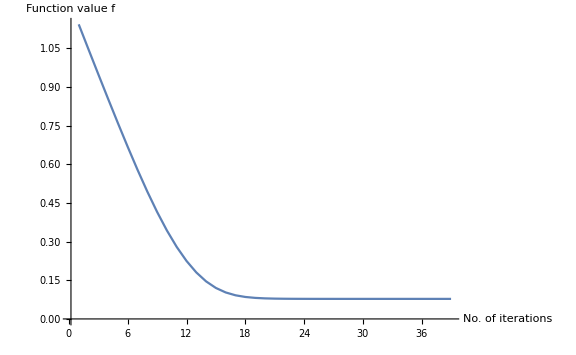

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```

## Bosonic Complexity of Purification (CoP)

```mathematica
L=100; (* number of lattice sites *)
l=1.; (* lattice spacing *)
m=.1; (* mass *)
dimA1=1; (* sites of subsystem A1 *)
dimB1=3; (* sites of subsystem B1 *)
d=5; (* distance between subsystem A1 and B1 *)
dimPur=dimA1+dimB1; (* dimensions of the purifying systm*)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=KGcmRes[{L,l,m},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimA2+dimB2,"qpqp"];
JR=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];

J0=JR;
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; (* Attention: For complexity, we need to put MTra, because JR transforms inversely to JT!!! *)
```

#### Consistency checks

```mathematica
J0.J0//Eigenvalues (*check J0 to describe pure bosonic state*)
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
MTra.CM0.Transpose[MTra]//Chop//MatrixForm (* check correct transformation *)
Cosh[2rlist]
```

(1.46243 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.46243 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.22221 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.22221 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.06604 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.06604 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.00032 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00032)

{1.46243,1.22221,1.06604,1.00032}

```mathematica
MTra.GOinvMSp[MTra]//Chop//MatrixForm (* check symplectic *)
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
rrlist={rlist⟦1⟧,rlist⟦2⟧,rlist⟦4⟧,rlist⟦3⟧}
CMback=Inverse[MTra].DiagonalMatrix[Cosh/@Flatten[Table[{2r,2r},{r,rlist}]]].Transpose[Inverse[MTra]];CMback//MatrixForm
CM0-CMback//Chop//MatrixForm
```

{0.464018,0.327439,0.0126183,0.180728}

(1.28101 | -1.10155×10^-16 | -0.00697557 | -1.97758×10^-16 | -0.0048107 | 4.74447×10^-16 | -0.00344953 | 1.04517×10^-16
-5.64056×10^-17 | 1.39418 | 3.4998×10^-16 | 0.247118 | -7.22512×10^-16 | 0.209989 | -2.07299×10^-16 | 0.179771
-0.00697557 | 3.50414×10^-16 | 1.28101 | -1.75554×10^-15 | -0.41982 | -4.46865×10^-15 | -0.0813337 | 1.45717×10^-16
-2.25514×10^-16 | 0.247118 | -1.75554×10^-15 | 1.39418 | 4.01068×10^-15 | 0.760649 | -1.0339×10^-15 | 0.554542
-0.0048107 | -7.22512×10^-16 | -0.41982 | 4.01068×10^-15 | 1.28101 | 4.44089×10^-16 | -0.41982 | -3.35842×10^-15
4.76182×10^-16 | 0.209989 | -4.46865×10^-15 | 0.760649 | 4.44089×10^-16 | 1.39418 | 3.30291×10^-15 | 0.760649
-0.00344953 | -2.34621×10^-16 | -0.0813337 | -9.78384×10^-16 | -0.41982 | 3.30291×10^-15 | 1.28101 | 1.2837×10^-15
1.043×10^-16 | 0.179771 | 2.01228×10^-16 | 0.554542 | -3.35842×10^-15 | 0.760649 | 1.2837×10^-15 | 1.39418)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 1. Define the problem-specific input arguments

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
M0List=Table[MatrixExp[RandomReal[{0,0.7},Length[LieBasis]].LieBasis].M0,{i,10}];
geometry=GOGeometryConst[LieBasis,J0,+1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 2.04239 seconds

Final value: 0.980472

Number of iterations: 7

Number of total corrections: 1

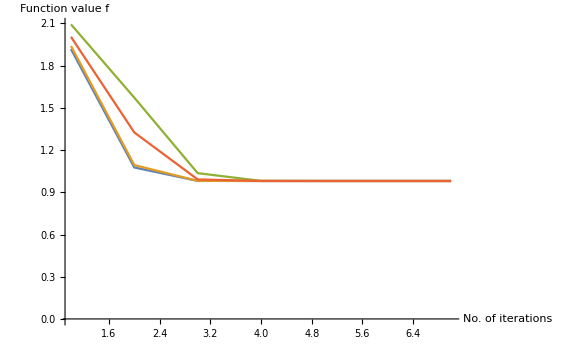

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```

## Fermionic Entanglement of Purification (EoP)

```mathematica
L=100; (* Total number lattice sites *)
J=2;h=2;γ=1; (* XY model parameter*)
dimA1=1; dimB1=3; (* dofs of chosen subystems *)
d=10; (* distance subsystems *)
dimA2=dimA1;dimB2= dimB1; (* purifying dofs, dimA2+dimB2 ≥ dimA1+dimB1 *)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=XYcmRes[{L,J,h,γ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormΩ[CM0];
J0=GOPurifyStandardJFermion[rlist,dimA2+dimB2,"qpqp"];
M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimA2+2dimB2]}}]//SparseArray;
```

### 1. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPFerm[Restriction];
gradient=GOEoPgradFerm[Restriction];

ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSO[dimA2+dimB2]}];
M0List=Table[MatrixExp[RandomReal[{0,0.2},Length[LieBasis]].LieBasis].M0,{i,100}];
```

```mathematica
geometry=GOGeometryConst[LieBasis,J0,-1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];

SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 4.28125 seconds

Final value: 0.216336

Number of iterations: 61

Number of total corrections: 185

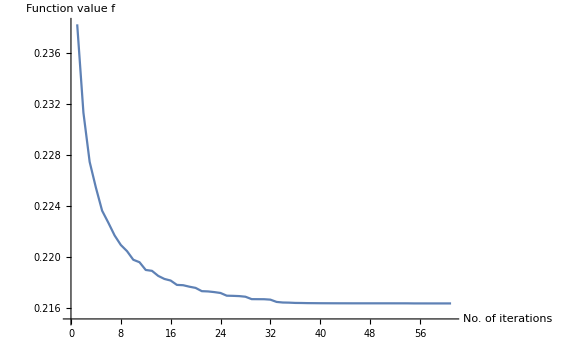

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```

## Fermionic Complexity of Purification (CoP)

```mathematica
L=12; (* Total number lattice sites *)
J=1;h=1;γ=1; (* XY model parameter*)
dimA1=2; dimB1=2; (* dofs of chosen subystems *)
d=0; (* distance subsystems *)
dimPur=dimA1+dimB1; (* dimensions of the purifying system*)
```

```mathematica
L=12; (* Total number lattice sites *)
J=4;h=1;γ=.9; (* XY model parameter*)
dimA1=2; dimB1=2; (* dofs of chosen subystems *)
d=4; (* distance subsystems *)
dimPur=dimA1+dimB1; (* dimensions of the purifying system*)

TT=GOqpqpFROMqqpp[L];

IND=Join[Table[i,{i,dimA1}],Table[i+dimA1+d,{i,dimB1}]];

(TT.XYcm[{L,J,h,γ}].Transpose[TT])⟦IND,IND⟧//MatrixForm;
Reverse[XYft[{L,J,h,γ}]]

(TT.XYcm[{L,J,h,γ}].Transpose[TT])//MatrixForm
XYcmRes[{L,J,h,γ},{dimA1,dimB1,d}]//MatrixForm

JJ=XYcm[{L,J,h,γ}];

JJ.JJ//MatrixForm;
```

{-0.129257,-0.0179652,0.00234356,-0.000145894,-0.000032918,0.0000404053,0.0000582762,-0.00105908,0.0045533,0.000252232,-0.131539,0.98267}

(0. | 0.129257 | 0. | 0.0179652 | 0. | -0.00234356 | 0. | 0.000145894 | 0. | 0.000032918 | 0. | -0.0000404053 | 0. | -0.0000582762 | 0. | 0.00105908 | 0. | -0.0045533 | 0. | -0.000252232 | 0. | 0.131539 | 0. | -0.98267
-0.129257 | 0. | -0.98267 | 0. | 0.131539 | 0. | -0.000252232 | 0. | -0.0045533 | 0. | 0.00105908 | 0. | -0.0000582762 | 0. | -0.0000404053 | 0. | 0.000032918 | 0. | 0.000145894 | 0. | -0.00234356 | 0. | 0.0179652 | 0.
0. | 0.98267 | 0. | 0.129257 | 0. | 0.0179652 | 0. | -0.00234356 | 0. | 0.000145894 | 0. | 0.000032918 | 0. | -0.0000404053 | 0. | -0.0000582762 | 0. | 0.00105908 | 0. | -0.0045533 | 0. | -0.000252232 | 0. | 0.131539
-0.0179652 | 0. | -0.129257 | 0. | -0.98267 | 0. | 0.131539 | 0. | -0.000252232 | 0. | -0.0045533 | 0. | 0.00105908 | 0. | -0.0000582762 | 0. | -0.0000404053 | 0. | 0.000032918 | 0. | 0.000145894 | 0. | -0.00234356 | 0.
0. | -0.131539 | 0. | 0.98267 | 0. | 0.129257 | 0. | 0.0179652 | 0. | -0.00234356 | 0. | 0.000145894 | 0. | 0.000032918 | 0. | -0.0000404053 | 0. | -0.0000582762 | 0. | 0.00105908 | 0. | -0.0045533 | 0. | -0.000252232
0.00234356 | 0. | -0.0179652 | 0. | -0.129257 | 0. | -0.98267 | 0. | 0.131539 | 0. | -0.000252232 | 0. | -0.0045533 | 0. | 0.00105908 | 0. | -0.0000582762 | 0. | -0.0000404053 | 0. | 0.000032918 | 0. | 0.000145894 | 0.
0. | 0.000252232 | 0. | -0.131539 | 0. | 0.98267 | 0. | 0.129257 | 0. | 0.0179652 | 0. | -0.00234356 | 0. | 0.000145894 | 0. | 0.000032918 | 0. | -0.0000404053 | 0. | -0.0000582762 | 0. | 0.00105908 | 0. | -0.0045533
-0.000145894 | 0. | 0.00234356 | 0. | -0.0179652 | 0. | -0.129257 | 0. | -0.98267 | 0. | 0.131539 | 0. | -0.000252232 | 0. | -0.0045533 | 0. | 0.00105908 | 0. | -0.0000582762 | 0. | -0.0000404053 | 0. | 0.000032918 | 0.
0. | 0.0045533 | 0. | 0.000252232 | 0. | -0.131539 | 0. | 0.98267 | 0. | 0.129257 | 0. | 0.0179652 | 0. | -0.00234356 | 0. | 0.000145894 | 0. | 0.000032918 | 0. | -0.0000404053 | 0. | -0.0000582762 | 0. | 0.00105908
-0.000032918 | 0. | -0.000145894 | 0. | 0.00234356 | 0. | -0.0179652 | 0. | -0.129257 | 0. | -0.98267 | 0. | 0.131539 | 0. | -0.000252232 | 0. | -0.0045533 | 0. | 0.00105908 | 0. | -0.0000582762 | 0. | -0.0000404053 | 0.
0. | -0.00105908 | 0. | 0.0045533 | 0. | 0.000252232 | 0. | -0.131539 | 0. | 0.98267 | 0. | 0.129257 | 0. | 0.0179652 | 0. | -0.00234356 | 0. | 0.000145894 | 0. | 0.000032918 | 0. | -0.0000404053 | 0. | -0.0000582762
0.0000404053 | 0. | -0.000032918 | 0. | -0.000145894 | 0. | 0.00234356 | 0. | -0.0179652 | 0. | -0.129257 | 0. | -0.98267 | 0. | 0.131539 | 0. | -0.000252232 | 0. | -0.0045533 | 0. | 0.00105908 | 0. | -0.0000582762 | 0.
0. | 0.0000582762 | 0. | -0.00105908 | 0. | 0.0045533 | 0. | 0.000252232 | 0. | -0.131539 | 0. | 0.98267 | 0. | 0.129257 | 0. | 0.0179652 | 0. | -0.00234356 | 0. | 0.000145894 | 0. | 0.000032918 | 0. | -0.0000404053
0.0000582762 | 0. | 0.0000404053 | 0. | -0.000032918 | 0. | -0.000145894 | 0. | 0.00234356 | 0. | -0.0179652 | 0. | -0.129257 | 0. | -0.98267 | 0. | 0.131539 | 0. | -0.000252232 | 0. | -0.0045533 | 0. | 0.00105908 | 0.
0. | 0.0000404053 | 0. | 0.0000582762 | 0. | -0.00105908 | 0. | 0.0045533 | 0. | 0.000252232 | 0. | -0.131539 | 0. | 0.98267 | 0. | 0.129257 | 0. | 0.0179652 | 0. | -0.00234356 | 0. | 0.000145894 | 0. | 0.000032918
-0.00105908 | 0. | 0.0000582762 | 0. | 0.0000404053 | 0. | -0.000032918 | 0. | -0.000145894 | 0. | 0.00234356 | 0. | -0.0179652 | 0. | -0.129257 | 0. | -0.98267 | 0. | 0.131539 | 0. | -0.000252232 | 0. | -0.0045533 | 0.
0. | -0.000032918 | 0. | 0.0000404053 | 0. | 0.0000582762 | 0. | -0.00105908 | 0. | 0.0045533 | 0. | 0.000252232 | 0. | -0.131539 | 0. | 0.98267 | 0. | 0.129257 | 0. | 0.0179652 | 0. | -0.00234356 | 0. | 0.000145894
0.0045533 | 0. | -0.00105908 | 0. | 0.0000582762 | 0. | 0.0000404053 | 0. | -0.000032918 | 0. | -0.000145894 | 0. | 0.00234356 | 0. | -0.0179652 | 0. | -0.129257 | 0. | -0.98267 | 0. | 0.131539 | 0. | -0.000252232 | 0.
0. | -0.000145894 | 0. | -0.000032918 | 0. | 0.0000404053 | 0. | 0.0000582762 | 0. | -0.00105908 | 0. | 0.0045533 | 0. | 0.000252232 | 0. | -0.131539 | 0. | 0.98267 | 0. | 0.129257 | 0. | 0.0179652 | 0. | -0.00234356
0.000252232 | 0. | 0.0045533 | 0. | -0.00105908 | 0. | 0.0000582762 | 0. | 0.0000404053 | 0. | -0.000032918 | 0. | -0.000145894 | 0. | 0.00234356 | 0. | -0.0179652 | 0. | -0.129257 | 0. | -0.98267 | 0. | 0.131539 | 0.
0. | 0.00234356 | 0. | -0.000145894 | 0. | -0.000032918 | 0. | 0.0000404053 | 0. | 0.0000582762 | 0. | -0.00105908 | 0. | 0.0045533 | 0. | 0.000252232 | 0. | -0.131539 | 0. | 0.98267 | 0. | 0.129257 | 0. | 0.0179652
-0.131539 | 0. | 0.000252232 | 0. | 0.0045533 | 0. | -0.00105908 | 0. | 0.0000582762 | 0. | 0.0000404053 | 0. | -0.000032918 | 0. | -0.000145894 | 0. | 0.00234356 | 0. | -0.0179652 | 0. | -0.129257 | 0. | -0.98267 | 0.
0. | -0.0179652 | 0. | 0.00234356 | 0. | -0.000145894 | 0. | -0.000032918 | 0. | 0.0000404053 | 0. | 0.0000582762 | 0. | -0.00105908 | 0. | 0.0045533 | 0. | 0.000252232 | 0. | -0.131539 | 0. | 0.98267 | 0. | 0.129257
0.98267 | 0. | -0.131539 | 0. | 0.000252232 | 0. | 0.0045533 | 0. | -0.00105908 | 0. | 0.0000582762 | 0. | 0.0000404053 | 0. | -0.000032918 | 0. | -0.000145894 | 0. | 0.00234356 | 0. | -0.0179652 | 0. | -0.129257 | 0.)

(0. | -0.129257 | 0. | 0.0179652 | 0. | -0.0000582762 | 0. | 0.00105908
0.129257 | 0. | -0.98267 | 0. | -0.0000582762 | 0. | -0.0000404053 | 0.
0. | 0.98267 | 0. | -0.129257 | 0. | -0.0000404053 | 0. | -0.0000582762
-0.0179652 | 0. | 0.129257 | 0. | 0.00105908 | 0. | -0.0000582762 | 0.
0. | 0.0000582762 | 0. | -0.00105908 | 0. | -0.129257 | 0. | 0.0179652
0.0000582762 | 0. | 0.0000404053 | 0. | 0.129257 | 0. | -0.98267 | 0.
0. | 0.0000404053 | 0. | 0.0000582762 | 0. | 0.98267 | 0. | -0.129257
-0.00105908 | 0. | 0.0000582762 | 0. | -0.0179652 | 0. | 0.129257 | 0.)

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=XYcmRes[{L,J,h,γ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormΩ[CM0];

JT=GOPurifyStandardJFermion[rlist,dimPur,"qpqp"];
JR=GOTransformΩtoJ[GOΩqpqp[dimA1+dimB1+dimPur],"qpqp","qpqp"]; (* reference state *)

J0=JR;
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; (* Attention: For complexity, we need to put MTra, because JR transforms inversely to JT!!! *)
```

#### Consistency checks

```mathematica
CM0.CM0//Eigenvalues
```

{-0.999377,-0.999377,-0.999377,-0.999377,-1.94768×10^-6,-1.94768×10^-6,-1.94768×10^-6,-1.94768×10^-6}

```mathematica
MTra.CM0.MTra//Chop//MatrixForm (* check correct transformation *)
rlist
J0//MatrixForm
```

(-0.000146704 | 0.130391 | -0.0000191013 | -0.0173661 | -0.00106093 | -0.982519 | -0.000139715 | 0.129336
-0.129372 | -0.000127798 | 0.982793 | -0.000969968 | 0.0170921 | -0.0000575782 | -0.12831 | -0.000438801
0.0468605 | 0.0000564859 | 0.00636971 | -7.22119×10^-6 | -0.990025 | 0.00106953 | -0.130341 | -0.00014083
0.000133178 | -0.107026 | -0.00101201 | -0.812001 | -0.0000437182 | -0.0746645 | 0.000330493 | -0.568331
0.0000176199 | -0.0000704249 | -0.000132274 | -0.00053606 | 0.00013318 | 0.000100902 | -0.00101172 | 0.00076554
0.000115405 | -0.00136683 | 0.0000151935 | 0.000179925 | 5.18844×10^-6 | -0.000181417 | 7.06428×10^-7 | 0.0000241619
-0.0000160902 | -0.0000768441 | 0.000120786 | -0.000584923 | -0.000121992 | 0.000110193 | 0.000926727 | 0.00083603
-0.00137728 | -0.000114553 | -0.000181324 | 0.0000150794 | -0.0000652129 | -0.0000149264 | -8.86423×10^-6 | 1.98839×10^-6)

{0.012486,0.012486,0.7847,0.7847}

(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
MTra.Transpose[MTra]//Chop//MatrixForm (* check orthogonal *)
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

### 1. Define the problem-specific input arguments

```mathematica
function=GOCoPFerm[JT]; gradient=GOCoPgradFerm[JT];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSONoUN[dimPur]}];
M0List=Table[MatrixExp[RandomReal[{0,0.7},Length[LieBasis]].LieBasis].M0,{i,10}];
geometry=GOGeometryConst[LieBasis,J0,-1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

$Aborted

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```

Reason for termination: Private`stopreason$177651

Time taken: 0.28125 seconds

Part::partw: Part 1 of {} does not exist.

Final value: {{},{},{},{},{{1/(2 √2)Re[√Total[Eigenvalues[ⅈ (Log[{{0.,0.991443,0.,-0.130537,0.,0.0010207,0.,-0.000334561,0.,0.,0.,0.,0.,0.,0.,0.},{0.130537,0.,-0.991443,0.,-0.0000581021,0.,-0.00107904,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0010207,0.,0.000334561,0.,0.991443,0.,-0.130537,0.,0.,0.,0.,0.,0.,0.,0.},{0.0000581021,0.,0.00107904,0.,0.130537,0.,-0.991443,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98798,0.,0.130098,0.,-0.0828013,0.,-0.0107024,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0963935,0.,0.731093,0.,0.0880239,0.,0.669673,0.,0.,0.,0.,0.,0.,0.,0.},{0.0828013,0.,0.0107024,0.,0.98798,0.,0.130098,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0880239,0.,-0.669673,0.,0.0963935,0.,0.731093,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.745191,-0.0671183,-0.153713,0.108477,0.033598,-0.113456,0.117636,0.613963},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0167051,0.86456,-0.179743,0.161823,-0.177668,0.148445,-0.34536,0.144522},{0.,0.,0.,0.,0.,0.,0.,0.,-0.357577,-0.0136877,0.57102,-0.0650868,0.033914,0.357292,0.0592073,0.639796},{0.,0.,0.,0.,0.,0.,0.,0.,0.0457365,-0.42558,0.0677339,0.517459,-0.196396,0.156179,-0.693872,-0.00395001},{0.,0.,0.,0.,0.,0.,0.,0.,-0.42644,-0.0575655,-0.481738,0.483682,0.513971,-0.0658997,0.159237,0.234413},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0891566,-0.214355,-0.546421,-0.610786,0.0244429,0.383565,-0.304872,0.183849},{0.,0.,0.,0.,0.,0.,0.,0.,0.00350534,-0.0851827,-0.233572,0.278775,-0.536029,0.549217,0.51342,-0.0888466},{0.,0.,0.,0.,0.,0.,0.,0.,-0.353051,-0.101028,-0.167958,-0.0729516,-0.612774,-0.599949,0.00453192,0.310105}}.SparseArray[IdentityMatrix[2 (4+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2 (4+dimA2+dimB2)]]].{{-0.130496,0.,-0.000058084,0.,0.,0.00137882,0.,0.000115557,0.00325944,0.,1.45078×10^-6,0.,0.,0.987979,0.,0.0828012},{0.,0.991134,0.,-0.00102038,-0.000134526,0.,0.000122846,0.,0.,0.0247558,0.,-0.0000254863,0.0963934,0.,-0.0880238,0.},{0.991134,0.,-0.0010787,0.,0.,0.000181563,0.,0.0000149362,-0.0247558,0.,0.0000269431,0.,0.,0.130097,0.,0.0107024},{0.,-0.130496,0.,0.000334456,-0.00102031,0.,0.000934592,0.,0.,-0.00325943,0.,8.35381×10^-6,0.731093,0.,-0.669673,0.},{0.000058084,0.,-0.130496,0.,0.,-0.000115557,0.,0.00137882,-1.45078×10^-6,0.,0.00325944,0.,0.,-0.0828012,0.,0.987979},{0.,0.00102038,0.,0.991134,-0.000122846,0.,-0.000134526,0.,0.,0.0000254863,0.,0.0247558,0.0880238,0.,0.0963934,0.},{0.0010787,0.,0.991134,0.,0.,-0.0000149362,0.,0.000181563,-0.0000269431,0.,-0.0247558,0.,0.,-0.0107024,0.,0.130097},{0.,-0.000334456,0.,-0.130496,-0.000934592,0.,-0.00102031,0.,0.,-8.35381×10^-6,0.,-0.00325943,0.669673,0.,0.731093,0.},{0.000417118,-0.0186071,-0.00114202,0.00892851,0.0891565,0.42644,0.353051,-0.00350534,0.0166999,0.744959,-0.0457223,-0.357465,0.000124426,-0.000595138,0.000492716,4.89203×10^-6},{-0.0215876,0.00167591,0.0106265,0.000341775,0.214354,0.0575654,0.101028,0.0851826,-0.864291,-0.0670974,0.425448,-0.0136834,0.000299152,-0.000080338,0.000140993,-0.00011888},{0.0044881,0.00383815,-0.00169128,-0.0142581,0.546421,0.481737,0.167958,0.233572,0.179687,-0.153665,-0.0677128,0.570842,0.000762582,-0.00067231,0.000234402,-0.000325972},{-0.00404063,-0.00270862,-0.0129207,0.00162518,0.610786,-0.483682,0.0729515,-0.278775,-0.161772,0.108443,-0.517298,-0.0650665,0.000852409,0.000675024,0.000101811,0.000389057},{0.00443627,-0.000838924,0.00490392,-0.000846815,-0.0244429,-0.51397,0.612774,0.536029,0.177612,0.0335875,0.196335,0.0339034,-0.0000341124,0.000717294,0.000855184,-0.000748079},{-0.00370661,0.00283294,-0.00389971,-0.0089214,-0.383565,0.0658996,0.599948,-0.549216,-0.148399,-0.113421,-0.15613,0.357181,-0.000535301,-0.0000919692,0.000837284,0.000766483},{0.00862346,-0.00293731,0.0173256,-0.00147838,0.304872,-0.159237,-0.00453191,-0.513419,0.345252,0.117599,0.693656,0.0591888,0.000425478,0.000222231,-6.32471×10^-6,0.000716525},{-0.00360865,-0.0153303,0.0000986297,-0.0159754,-0.183849,-0.234413,-0.310105,0.0888465,-0.144477,0.613771,0.00394878,0.639596,-0.000256578,0.000327145,-0.000432781,-0.000123994}}])^2]]]},{1/(2 √2)Re[√Total[Eigenvalues[ⅈ (Log[{{0.,0.991443,0.,-0.130537,0.,0.0010207,0.,-0.000334561,0.,0.,0.,0.,0.,0.,0.,0.},{0.130537,0.,-0.991443,0.,-0.0000581021,0.,-0.00107904,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0010207,0.,0.000334561,0.,0.991443,0.,-0.130537,0.,0.,0.,0.,0.,0.,0.,0.},{0.0000581021,0.,0.00107904,0.,0.130537,0.,-0.991443,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98798,0.,0.130098,0.,-0.0828013,0.,-0.0107024,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0963935,0.,0.731093,0.,0.0880239,0.,0.669673,0.,0.,0.,0.,0.,0.,0.,0.},{0.0828013,0.,0.0107024,0.,0.98798,0.,0.130098,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0880239,0.,-0.669673,0.,0.0963935,0.,0.731093,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.643028,-0.0415317,-0.196824,-0.0303198,0.185506,0.391067,0.304826,0.514653},{0.,0.,0.,0.,0.,0.,0.,0.,0.0231993,0.432185,-0.108255,0.0608008,-0.454371,0.45066,-0.604899,0.147686},{0.,0.,0.,0.,0.,0.,0.,0.,-0.42827,0.0620692,0.688075,-0.12698,0.169089,0.355241,0.125082,0.390804},{0.,0.,0.,0.,0.,0.,0.,0.,-0.130458,-0.694201,-0.0659304,0.498564,0.127947,0.0920108,-0.408729,0.237189},{0.,0.,0.,0.,0.,0.,0.,0.,-0.405329,0.446854,-0.479802,0.215777,0.546895,-0.0768568,0.0000858608,0.232933},{0.,0.,0.,0.,0.,0.,0.,0.,-0.361411,-0.343554,-0.448131,-0.572028,-0.0285269,0.440436,0.0761393,-0.150732},{0.,0.,0.,0.,0.,0.,0.,0.,-0.253083,0.018303,-0.135957,0.532369,-0.484894,0.211833,0.593356,-0.0405689},{0.,0.,0.,0.,0.,0.,0.,0.,-0.163041,-0.0876416,-0.1491,-0.271113,-0.423251,-0.514341,0.0245954,0.652465}}.SparseArray[IdentityMatrix[2 (4+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2 (4+dimA2+dimB2)]]].{{-0.130496,0.,-0.000058084,0.,0.,0.00137882,0.,0.000115557,0.00325944,0.,1.45078×10^-6,0.,0.,0.987979,0.,0.0828012},{0.,0.991134,0.,-0.00102038,-0.000134526,0.,0.000122846,0.,0.,0.0247558,0.,-0.0000254863,0.0963934,0.,-0.0880238,0.},{0.991134,0.,-0.0010787,0.,0.,0.000181563,0.,0.0000149362,-0.0247558,0.,0.0000269431,0.,0.,0.130097,0.,0.0107024},{0.,-0.130496,0.,0.000334456,-0.00102031,0.,0.000934592,0.,0.,-0.00325943,0.,8.35381×10^-6,0.731093,0.,-0.669673,0.},{0.000058084,0.,-0.130496,0.,0.,-0.000115557,0.,0.00137882,-1.45078×10^-6,0.,0.00325944,0.,0.,-0.0828012,0.,0.987979},{0.,0.00102038,0.,0.991134,-0.000122846,0.,-0.000134526,0.,0.,0.0000254863,0.,0.0247558,0.0880238,0.,0.0963934,0.},{0.0010787,0.,0.991134,0.,0.,-0.0000149362,0.,0.000181563,-0.0000269431,0.,-0.0247558,0.,0.,-0.0107024,0.,0.130097},{0.,-0.000334456,0.,-0.130496,-0.000934592,0.,-0.00102031,0.,0.,-8.35381×10^-6,0.,-0.00325943,0.669673,0.,0.731093,0.},{-0.000579276,-0.0160561,0.00325746,0.0106937,0.361411,0.405329,0.163041,0.253083,-0.0231921,0.642827,0.130417,-0.428136,0.000504383,-0.000565675,0.000227539,-0.000353201},{-0.0107914,0.00103703,0.0173338,-0.00154984,0.343554,-0.446854,0.0876415,-0.018303,-0.43205,-0.0415188,0.693984,0.0620499,0.000479462,0.000623627,0.000122312,0.0000255435},{0.00270307,0.00491459,0.00164625,-0.0171809,0.448131,0.479802,0.149099,0.135957,0.108221,-0.196762,0.0659098,0.687861,0.000625409,-0.000669609,0.000208082,-0.000189741},{-0.00151816,0.000757071,-0.0124489,0.00317063,0.572028,-0.215777,0.271112,-0.532368,-0.0607818,-0.0303104,-0.498408,-0.126941,0.000798319,0.000301137,0.000378363,0.00074297},{0.0113454,-0.00463199,-0.00319477,-0.00422207,0.0285269,-0.546895,0.423251,0.484894,0.45423,0.185448,-0.127907,0.169036,0.0000398119,0.000763244,0.000590687,-0.000676715},{-0.0112528,-0.00976474,-0.00229746,-0.0088702,-0.440435,0.0768568,0.51434,-0.211833,-0.45052,0.390945,-0.0919821,0.355131,-0.000614669,-0.000107261,0.00071781,0.000295633},{0.015104,-0.00761134,0.0102057,-0.00312323,-0.0761393,-0.0000858608,-0.0245954,-0.593356,0.604711,0.304731,0.408601,0.125043,-0.00010626,1.19827×10^-7,-0.0000343252,0.000828084},{-0.00368765,-0.0128506,-0.00592248,-0.00975818,0.150732,-0.232933,-0.652465,0.0405689,-0.14764,0.514492,-0.237115,0.390682,0.000210361,0.00032508,-0.000910576,-0.0000566177}}])^2]]]},{1/(2 √2)Re[√Total[Eigenvalues[ⅈ (Log[{{0.,0.991443,0.,-0.130537,0.,0.0010207,0.,-0.000334561,0.,0.,0.,0.,0.,0.,0.,0.},{0.130537,0.,-0.991443,0.,-0.0000581021,0.,-0.00107904,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0010207,0.,0.000334561,0.,0.991443,0.,-0.130537,0.,0.,0.,0.,0.,0.,0.,0.},{0.0000581021,0.,0.00107904,0.,0.130537,0.,-0.991443,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98798,0.,0.130098,0.,-0.0828013,0.,-0.0107024,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0963935,0.,0.731093,0.,0.0880239,0.,0.669673,0.,0.,0.,0.,0.,0.,0.,0.},{0.0828013,0.,0.0107024,0.,0.98798,0.,0.130098,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0880239,0.,-0.669673,0.,0.0963935,0.,0.731093,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.595904,0.103515,0.205938,0.240625,0.27562,0.284586,0.517739,0.329945},{0.,0.,0.,0.,0.,0.,0.,0.,0.205523,0.851852,-0.0786005,-0.0341656,-0.347931,0.0391257,-0.286433,0.141891},{0.,0.,0.,0.,0.,0.,0.,0.,-0.451193,0.0603145,0.726516,-0.112637,-0.134724,-0.0463057,0.0635344,0.477433},{0.,0.,0.,0.,0.,0.,0.,0.,0.0868921,-0.334447,0.00956943,0.693768,-0.404469,0.179929,-0.388592,0.22851},{0.,0.,0.,0.,0.,0.,0.,0.,-0.53578,0.287306,-0.371345,0.435513,0.481566,0.0344513,0.066332,0.255604},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0445372,-0.14171,-0.146616,-0.430633,0.164553,0.753179,-0.329671,0.260679},{0.,0.,0.,0.,0.,0.,0.,0.,-0.287701,0.0102241,-0.266347,-0.0148099,-0.583279,0.349588,0.61362,-0.0837139},{0.,0.,0.,0.,0.,0.,0.,0.,0.14042,-0.213095,-0.4395,-0.267573,-0.148442,-0.438502,0.0724533,0.67123}}.SparseArray[IdentityMatrix[2 (4+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2 (4+dimA2+dimB2)]]].{{-0.130496,0.,-0.000058084,0.,0.,0.00137882,0.,0.000115557,0.00325944,0.,1.45078×10^-6,0.,0.,0.987979,0.,0.0828012},{0.,0.991134,0.,-0.00102038,-0.000134526,0.,0.000122846,0.,0.,0.0247558,0.,-0.0000254863,0.0963934,0.,-0.0880238,0.},{0.991134,0.,-0.0010787,0.,0.,0.000181563,0.,0.0000149362,-0.0247558,0.,0.0000269431,0.,0.,0.130097,0.,0.0107024},{0.,-0.130496,0.,0.000334456,-0.00102031,0.,0.000934592,0.,0.,-0.00325943,0.,8.35381×10^-6,0.731093,0.,-0.669673,0.},{0.000058084,0.,-0.130496,0.,0.,-0.000115557,0.,0.00137882,-1.45078×10^-6,0.,0.00325944,0.,0.,-0.0828012,0.,0.987979},{0.,0.00102038,0.,0.991134,-0.000122846,0.,-0.000134526,0.,0.,0.0000254863,0.,0.0247558,0.0880238,0.,0.0963934,0.},{0.0010787,0.,0.991134,0.,0.,-0.0000149362,0.,0.000181563,-0.0000269431,0.,-0.0247558,0.,0.,-0.0107024,0.,0.130097},{0.,-0.000334456,0.,-0.130496,-0.000934592,0.,-0.00102031,0.,0.,-8.35381×10^-6,0.,-0.00325943,0.669673,0.,0.731093,0.},{-0.0051318,-0.0148794,-0.00216965,0.0112661,0.0445372,0.535779,-0.14042,0.287701,-0.205459,0.595718,-0.086865,-0.451052,0.0000621558,-0.000747731,-0.000195969,-0.000401514},{-0.0212703,-0.00258471,0.00835097,-0.00150602,0.14171,-0.287306,0.213095,-0.0102241,-0.851586,0.103483,0.334343,0.0602957,0.00019777,0.000400962,0.000297394,0.0000142687},{0.00196261,-0.00514216,-0.000238944,-0.0181407,0.146616,0.371345,0.439499,0.266347,0.078576,0.205874,-0.00956644,0.72629,0.000204616,-0.000518247,0.000613363,-0.000371712},{0.000853097,-0.00600829,-0.017323,0.0028125,0.430633,-0.435513,0.267573,0.0148099,0.0341549,0.24055,-0.693551,-0.112602,0.000600989,0.0006078,0.000373423,-0.0000206686},{0.00868765,-0.00688208,0.0100994,0.00336398,-0.164552,-0.481566,0.148442,0.583278,0.347822,0.275534,0.404343,-0.134682,-0.000229648,0.000672071,0.000207165,-0.00081402},{-0.000976949,-0.00710596,-0.00449274,0.00115623,-0.753179,-0.0344513,0.438501,-0.349588,-0.0391135,0.284497,-0.179873,-0.0462912,-0.00105113,0.00004808,0.00061197,0.000487883},{0.0071521,-0.0129277,0.00970295,-0.00158642,0.329671,-0.066332,-0.0724533,-0.613619,0.286344,0.517577,0.388471,0.0635146,0.000460087,0.0000925726,-0.000101115,0.000856364},{-0.00354294,-0.00823856,-0.00570577,-0.0119213,-0.260679,-0.255604,-0.671229,0.0837138,-0.141847,0.329842,-0.228438,0.477284,-0.000363802,0.000356719,-0.000936764,-0.000116831}}])^2]]]},{1/(2 √2)Re[√Total[Eigenvalues[ⅈ (Log[{{0.,0.991443,0.,-0.130537,0.,0.0010207,0.,-0.000334561,0.,0.,0.,0.,0.,0.,0.,0.},{0.130537,0.,-0.991443,0.,-0.0000581021,0.,-0.00107904,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0010207,0.,0.000334561,0.,0.991443,0.,-0.130537,0.,0.,0.,0.,0.,0.,0.,0.},{0.0000581021,0.,0.00107904,0.,0.130537,0.,-0.991443,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98798,0.,0.130098,0.,-0.0828013,0.,-0.0107024,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0963935,0.,0.731093,0.,0.0880239,0.,0.669673,0.,0.,0.,0.,0.,0.,0.,0.},{0.0828013,0.,0.0107024,0.,0.98798,0.,0.130098,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0880239,0.,-0.669673,0.,0.0963935,0.,0.731093,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.582572,-0.0530579,0.286718,0.238819,0.16726,0.36456,0.34299,0.489929},{0.,0.,0.,0.,0.,0.,0.,0.,0.0118459,0.30263,0.0645016,0.163717,-0.4101,-0.0400179,-0.654103,0.528845},{0.,0.,0.,0.,0.,0.,0.,0.,-0.680237,0.0922268,0.513779,-0.193204,-0.093628,0.16353,0.321777,0.297367},{0.,0.,0.,0.,0.,0.,0.,0.,-0.346937,-0.643788,-0.152213,0.645933,-0.0251932,0.0986009,-0.0673416,0.0994108},{0.,0.,0.,0.,0.,0.,0.,0.,-0.258057,0.46582,-0.338958,0.250004,0.682072,-0.0933978,0.0234514,0.254024},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0935624,-0.0990997,-0.459966,-0.405748,0.0187081,0.752493,-0.160458,0.113501},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0205534,0.31569,-0.470168,0.221835,-0.572957,-0.0039619,0.547426,0.0409577},{0.,0.,0.,0.,0.,0.,0.,0.,0.0401545,-0.395173,-0.281026,-0.43042,0.0242768,-0.504029,0.143035,0.550359}}.SparseArray[IdentityMatrix[2 (4+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2 (4+dimA2+dimB2)]]].{{-0.130496,0.,-0.000058084,0.,0.,0.00137882,0.,0.000115557,0.00325944,0.,1.45078×10^-6,0.,0.,0.987979,0.,0.0828012},{0.,0.991134,0.,-0.00102038,-0.000134526,0.,0.000122846,0.,0.,0.0247558,0.,-0.0000254863,0.0963934,0.,-0.0880238,0.},{0.991134,0.,-0.0010787,0.,0.,0.000181563,0.,0.0000149362,-0.0247558,0.,0.0000269431,0.,0.,0.130097,0.,0.0107024},{0.,-0.130496,0.,0.000334456,-0.00102031,0.,0.000934592,0.,0.,-0.00325943,0.,8.35381×10^-6,0.731093,0.,-0.669673,0.},{0.000058084,0.,-0.130496,0.,0.,-0.000115557,0.,0.00137882,-1.45078×10^-6,0.,0.00325944,0.,0.,-0.0828012,0.,0.987979},{0.,0.00102038,0.,0.991134,-0.000122846,0.,-0.000134526,0.,0.,0.0000254863,0.,0.0247558,0.0880238,0.,0.0963934,0.},{0.0010787,0.,0.991134,0.,0.,-0.0000149362,0.,0.000181563,-0.0000269431,0.,-0.0247558,0.,0.,-0.0107024,0.,0.130097},{0.,-0.000334456,0.,-0.130496,-0.000934592,0.,-0.00102031,0.,0.,-8.35381×10^-6,0.,-0.00325943,0.669673,0.,0.731093,0.},{-0.000295787,-0.0145465,0.00866284,0.0169852,0.0935623,0.258057,-0.0401545,0.0205534,-0.0118423,0.582391,0.346829,-0.680024,0.000130575,-0.000360142,-0.0000560394,-0.0000286842},{-0.00755651,0.00132483,0.0160751,-0.00230286,0.0990996,-0.46582,0.395173,-0.31569,-0.302535,-0.0530414,0.643587,0.092198,0.000138303,0.000650096,0.000551501,0.000440575},{-0.00161057,-0.0071592,0.00380068,-0.0128288,0.459965,0.338957,0.281026,0.470168,-0.0644815,0.286628,0.152165,0.513619,0.000641925,-0.000473047,0.000392199,-0.000656164},{-0.00408792,-0.0059632,-0.0161286,0.0048242,0.405748,-0.250004,0.43042,-0.221834,-0.163666,0.238745,-0.645731,-0.193143,0.00056626,0.000348904,0.000600691,0.000309591},{0.01024,-0.0041764,0.000629062,0.00233784,-0.018708,-0.682072,-0.0242768,0.572956,0.409972,0.167208,0.0251854,-0.0935988,-0.0000261088,0.000951895,-0.0000338805,-0.000799614},{0.000999228,-0.00910288,-0.00246202,-0.00408327,-0.752492,0.0933977,0.504029,0.0039619,0.0400055,0.364446,-0.0985702,0.163479,-0.00105017,-0.000130345,0.00070342,-5.5292×10^-6},{0.0163326,-0.00856429,0.00168149,-0.0080346,0.160458,-0.0234514,-0.143035,-0.547426,0.653899,0.342883,0.0673206,0.321677,0.000223934,0.0000327286,-0.000199619,0.000763985},{-0.013205,-0.0122333,-0.00248224,-0.00742511,-0.113501,-0.254024,-0.550358,-0.0409577,-0.52868,0.489776,-0.0993798,0.297275,-0.000158401,0.000354514,-0.000768077,0.0000571603}}])^2]]]},{1/(2 √2)Re[√Total[Eigenvalues[ⅈ (Log[{{0.,0.991443,0.,-0.130537,0.,0.0010207,0.,-0.000334561,0.,0.,0.,0.,0.,0.,0.,0.},{0.130537,0.,-0.991443,0.,-0.0000581021,0.,-0.00107904,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0010207,0.,0.000334561,0.,0.991443,0.,-0.130537,0.,0.,0.,0.,0.,0.,0.,0.},{0.0000581021,0.,0.00107904,0.,0.130537,0.,-0.991443,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98798,0.,0.130098,0.,-0.0828013,0.,-0.0107024,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0963935,0.,0.731093,0.,0.0880239,0.,0.669673,0.,0.,0.,0.,0.,0.,0.,0.},{0.0828013,0.,0.0107024,0.,0.98798,0.,0.130098,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0880239,0.,-0.669673,0.,0.0963935,0.,0.731093,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.638508,-0.207798,-0.126309,0.298455,-0.0452432,0.32469,0.111079,0.569465},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0758788,0.550455,-0.0858129,0.0996583,-0.322765,0.40871,-0.629692,0.0788268},{0.,0.,0.,0.,0.,0.,0.,0.,-0.426487,0.13374,0.454457,-0.255713,0.263489,0.257743,0.173488,0.601952},{0.,0.,0.,0.,0.,0.,0.,0.,-0.454533,-0.69591,-0.100024,0.230543,-0.138241,-0.0336275,-0.428815,0.204526},{0.,0.,0.,0.,0.,0.,0.,0.,-0.327044,0.291947,-0.642168,0.400311,0.395597,-0.0996006,0.199388,0.170316},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0579212,-0.207412,-0.541192,-0.644044,-0.0170315,0.476614,0.104711,-0.086764},{0.,0.,0.,0.,0.,0.,0.,0.,-0.293118,0.0266147,0.0304962,0.265547,-0.684017,0.205556,0.570856,-0.076937},{0.,0.,0.,0.,0.,0.,0.,0.,0.042759,0.150604,-0.232265,-0.369995,-0.424939,-0.616957,-0.0239387,0.472085}}.SparseArray[IdentityMatrix[2 (4+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2 (4+dimA2+dimB2)]]].{{-0.130496,0.,-0.000058084,0.,0.,0.00137882,0.,0.000115557,0.00325944,0.,1.45078×10^-6,0.,0.,0.987979,0.,0.0828012},{0.,0.991134,0.,-0.00102038,-0.000134526,0.,0.000122846,0.,0.,0.0247558,0.,-0.0000254863,0.0963934,0.,-0.0880238,0.},{0.991134,0.,-0.0010787,0.,0.,0.000181563,0.,0.0000149362,-0.0247558,0.,0.0000269431,0.,0.,0.130097,0.,0.0107024},{0.,-0.130496,0.,0.000334456,-0.00102031,0.,0.000934592,0.,0.,-0.00325943,0.,8.35381×10^-6,0.731093,0.,-0.669673,0.},{0.000058084,0.,-0.130496,0.,0.,-0.000115557,0.,0.00137882,-1.45078×10^-6,0.,0.00325944,0.,0.,-0.0828012,0.,0.987979},{0.,0.00102038,0.,0.991134,-0.000122846,0.,-0.000134526,0.,0.,0.0000254863,0.,0.0247558,0.0880238,0.,0.0963934,0.},{0.0010787,0.,0.991134,0.,0.,-0.0000149362,0.,0.000181563,-0.0000269431,0.,-0.0247558,0.,0.,-0.0107024,0.,0.130097},{0.,-0.000334456,0.,-0.130496,-0.000934592,0.,-0.00102031,0.,0.,-8.35381×10^-6,0.,-0.00325943,0.669673,0.,0.731093,0.},{0.00189465,-0.0159432,0.0113495,0.0106492,0.0579211,0.327044,-0.0427589,0.293118,0.0758551,0.638308,0.454391,-0.426354,0.0000808344,-0.00045642,-0.0000596742,-0.000409074},{-0.0137446,0.00518861,0.0173765,-0.00333942,0.207412,-0.291947,-0.150604,-0.0266147,-0.550283,-0.207733,0.695693,0.133698,0.000289463,0.000407439,-0.000210182,0.0000371433},{0.0021427,0.00315386,0.00249755,-0.0113476,0.541192,0.642168,0.232265,-0.0304961,0.0857861,-0.126269,0.0999928,0.454315,0.000755285,-0.000896206,0.000324148,0.0000425603},{-0.00248842,-0.00745227,-0.00575654,0.00638503,0.644044,-0.400311,0.369994,-0.265547,-0.0996273,0.298362,-0.230471,-0.255634,0.000898824,0.000558671,0.000516362,0.000370596},{0.00805927,0.0011297,0.00345181,-0.00657919,0.0170315,-0.395597,0.424939,0.684016,0.322664,-0.0452291,0.138198,0.263407,0.0000237691,0.000552092,0.000593042,-0.000954609},{-0.0102053,-0.00810733,0.000839661,-0.00643572,-0.476613,0.0996005,0.616956,-0.205556,-0.408583,0.324588,0.033617,0.257663,-0.000665159,-0.000139002,0.000861021,0.000286873},{0.0157231,-0.0027736,0.0107073,-0.00433191,-0.104711,-0.199388,0.0239387,-0.570856,0.629495,0.111045,0.428681,0.173434,-0.000146133,0.000278264,0.0000334088,0.000796683},{-0.00196826,-0.0142192,-0.0051069,-0.0150304,0.0867639,-0.170316,-0.472085,0.0769369,-0.0788022,0.569287,-0.204462,0.601764,0.000121087,0.000237692,-0.000658839,-0.000107373}}])^2]]]},{1/(2 √2)Re[√Total[Eigenvalues[ⅈ (Log[{{0.,0.991443,0.,-0.130537,0.,0.0010207,0.,-0.000334561,0.,0.,0.,0.,0.,0.,0.,0.},{0.130537,0.,-0.991443,0.,-0.0000581021,0.,-0.00107904,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0010207,0.,0.000334561,0.,0.991443,0.,-0.130537,0.,0.,0.,0.,0.,0.,0.,0.},{0.0000581021,0.,0.00107904,0.,0.130537,0.,-0.991443,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98798,0.,0.130098,0.,-0.0828013,0.,-0.0107024,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0963935,0.,0.731093,0.,0.0880239,0.,0.669673,0.,0.,0.,0.,0.,0.,0.,0.},{0.0828013,0.,0.0107024,0.,0.98798,0.,0.130098,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0880239,0.,-0.669673,0.,0.0963935,0.,0.731093,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.681611,0.246342,0.208338,0.137118,0.478745,0.267583,0.201326,0.266808},{0.,0.,0.,0.,0.,0.,0.,0.,0.266901,0.459701,-0.301915,-0.105728,-0.282485,-0.0115188,-0.69545,0.226993},{0.,0.,0.,0.,0.,0.,0.,0.,-0.410978,0.311921,0.684702,-0.109764,-0.0982971,0.449349,-0.157707,0.128409},{0.,0.,0.,0.,0.,0.,0.,0.,-0.144219,-0.408829,0.019589,0.712454,0.191045,0.113228,-0.442816,0.242241},{0.,0.,0.,0.,0.,0.,0.,0.,-0.502233,0.503808,-0.483479,0.159182,0.402111,0.0857269,0.209523,0.148006},{0.,0.,0.,0.,0.,0.,0.,0.,0.00602733,-0.359209,-0.340716,-0.415119,0.204053,0.700916,-0.166775,-0.147602},{0.,0.,0.,0.,0.,0.,0.,0.,0.110231,0.0531198,-0.209302,0.383698,-0.657729,0.450811,0.391837,0.0679917},{0.,0.,0.,0.,0.,0.,0.,0.,-0.100213,-0.279068,-0.0509352,-0.324799,-0.0943814,-0.108026,0.172074,0.868218}}.SparseArray[IdentityMatrix[2 (4+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2 (4+dimA2+dimB2)]]].{{-0.130496,0.,-0.000058084,0.,0.,0.00137882,0.,0.000115557,0.00325944,0.,1.45078×10^-6,0.,0.,0.987979,0.,0.0828012},{0.,0.991134,0.,-0.00102038,-0.000134526,0.,0.000122846,0.,0.,0.0247558,0.,-0.0000254863,0.0963934,0.,-0.0880238,0.},{0.991134,0.,-0.0010787,0.,0.,0.000181563,0.,0.0000149362,-0.0247558,0.,0.0000269431,0.,0.,0.130097,0.,0.0107024},{0.,-0.130496,0.,0.000334456,-0.00102031,0.,0.000934592,0.,0.,-0.00325943,0.,8.35381×10^-6,0.731093,0.,-0.669673,0.},{0.000058084,0.,-0.130496,0.,0.,-0.000115557,0.,0.00137882,-1.45078×10^-6,0.,0.00325944,0.,0.,-0.0828012,0.,0.987979},{0.,0.00102038,0.,0.991134,-0.000122846,0.,-0.000134526,0.,0.,0.0000254863,0.,0.0247558,0.0880238,0.,0.0963934,0.},{0.0010787,0.,0.991134,0.,0.,-0.0000149362,0.,0.000181563,-0.0000269431,0.,-0.0247558,0.,0.,-0.0107024,0.,0.130097},{0.,-0.000334456,0.,-0.130496,-0.000934592,0.,-0.00102031,0.,0.,-8.35381×10^-6,0.,-0.00325943,0.669673,0.,0.731093,0.},{-0.00666438,-0.0170195,0.00360107,0.0102619,-0.00602732,0.502233,0.100213,-0.110231,-0.266818,0.681398,0.144174,-0.41085,-8.4117×10^-6,-0.000700914,0.000139857,0.000153838},{-0.0114785,-0.00615104,0.0102082,-0.00778851,0.359209,-0.503807,0.279068,-0.0531198,-0.459558,0.246266,0.408701,0.311824,0.00050131,0.000703111,0.000389465,0.0000741337},{0.00753867,-0.00520209,-0.000489127,-0.0170967,0.340716,0.483479,0.0509351,0.209302,0.301821,0.208273,-0.0195829,0.684489,0.000475501,-0.000674741,0.0000710848,-0.0002921},{0.00263998,-0.00342377,-0.0177896,0.00274076,0.415119,-0.159182,0.324799,-0.383697,0.105695,0.137075,-0.712232,-0.10973,0.000579338,0.000222153,0.000453287,0.000535486},{0.0070535,-0.011954,-0.00477031,0.00245443,-0.204053,-0.40211,0.0943813,0.657728,0.282397,0.478595,-0.190986,-0.0982665,-0.000284775,0.000561183,0.000131718,-0.000917922},{0.000287619,-0.00668141,-0.00282725,-0.01122,-0.700915,-0.0857268,0.108026,-0.45081,0.0115152,0.2675,-0.113193,0.449209,-0.000978193,0.00011964,0.000150761,0.000629148},{0.017365,-0.00502701,0.0110569,0.00393787,0.166774,-0.209523,-0.172074,-0.391836,0.695233,0.201263,0.442678,-0.157658,0.000232749,0.000292409,-0.000240145,0.000546845},{-0.0056679,-0.00666207,-0.00604864,-0.00320631,0.147602,-0.148006,-0.868217,-0.0679916,-0.226922,0.266725,-0.242166,0.128369,0.000205993,0.000206556,-0.00121168,0.0000948887}}])^2]]]},{1/(2 √2)Re[√Total[Eigenvalues[ⅈ (Log[{{0.,0.991443,0.,-0.130537,0.,0.0010207,0.,-0.000334561,0.,0.,0.,0.,0.,0.,0.,0.},{0.130537,0.,-0.991443,0.,-0.0000581021,0.,-0.00107904,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0010207,0.,0.000334561,0.,0.991443,0.,-0.130537,0.,0.,0.,0.,0.,0.,0.,0.},{0.0000581021,0.,0.00107904,0.,0.130537,0.,-0.991443,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98798,0.,0.130098,0.,-0.0828013,0.,-0.0107024,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0963935,0.,0.731093,0.,0.0880239,0.,0.669673,0.,0.,0.,0.,0.,0.,0.,0.},{0.0828013,0.,0.0107024,0.,0.98798,0.,0.130098,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0880239,0.,-0.669673,0.,0.0963935,0.,0.731093,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.456092,0.0321001,-0.0533791,0.16581,0.361077,0.249528,0.566294,0.49727},{0.,0.,0.,0.,0.,0.,0.,0.,0.241371,0.400795,-0.439483,0.213439,0.00435055,-0.164928,-0.598738,0.395846},{0.,0.,0.,0.,0.,0.,0.,0.,-0.616072,0.322471,0.265227,-0.321298,0.0582621,0.0808168,0.0177618,0.576757},{0.,0.,0.,0.,0.,0.,0.,0.,-0.312176,-0.600841,-0.101151,0.522019,-0.254977,0.261385,-0.121623,0.332677},{0.,0.,0.,0.,0.,0.,0.,0.,-0.455483,-0.0521504,-0.658362,0.0194186,0.519504,-0.128357,0.189048,-0.184116},{0.,0.,0.,0.,0.,0.,0.,0.,0.189092,-0.358903,-0.279503,-0.682324,0.043884,0.458021,-0.26797,0.0907134},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0580466,0.31954,-0.447699,-0.0726053,-0.695573,0.203751,0.401718,-0.0458872},{0.,0.,0.,0.,0.,0.,0.,0.,0.100661,-0.373762,-0.106918,-0.282844,-0.21346,-0.753597,0.191812,0.32935}}.SparseArray[IdentityMatrix[2 (4+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2 (4+dimA2+dimB2)]]].{{-0.130496,0.,-0.000058084,0.,0.,0.00137882,0.,0.000115557,0.00325944,0.,1.45078×10^-6,0.,0.,0.987979,0.,0.0828012},{0.,0.991134,0.,-0.00102038,-0.000134526,0.,0.000122846,0.,0.,0.0247558,0.,-0.0000254863,0.0963934,0.,-0.0880238,0.},{0.991134,0.,-0.0010787,0.,0.,0.000181563,0.,0.0000149362,-0.0247558,0.,0.0000269431,0.,0.,0.130097,0.,0.0107024},{0.,-0.130496,0.,0.000334456,-0.00102031,0.,0.000934592,0.,0.,-0.00325943,0.,8.35381×10^-6,0.731093,0.,-0.669673,0.},{0.000058084,0.,-0.130496,0.,0.,-0.000115557,0.,0.00137882,-1.45078×10^-6,0.,0.00325944,0.,0.,-0.0828012,0.,0.987979},{0.,0.00102038,0.,0.991134,-0.000122846,0.,-0.000134526,0.,0.,0.0000254863,0.,0.0247558,0.0880238,0.,0.0963934,0.},{0.0010787,0.,0.991134,0.,0.,-0.0000149362,0.,0.000181563,-0.0000269431,0.,-0.0247558,0.,0.,-0.0107024,0.,0.130097},{0.,-0.000334456,0.,-0.130496,-0.000934592,0.,-0.00102031,0.,0.,-8.35381×10^-6,0.,-0.00325943,0.669673,0.,0.731093,0.},{-0.0060269,-0.0113884,0.00779487,0.015383,-0.189092,0.455482,-0.10066,0.0580465,-0.241295,0.45595,0.312079,-0.61588,-0.000263896,-0.000635669,-0.000140481,-0.0000810094},{-0.0100076,-0.000801524,0.0150027,-0.00805194,0.358903,0.0521504,0.373762,-0.31954,-0.40067,0.0320901,0.600654,0.32237,0.000500883,-0.0000727808,0.00052162,0.000445948},{0.0109737,0.00133285,0.00252569,-0.00662258,0.279502,0.658362,0.106918,0.447698,0.439346,-0.0533625,0.101119,0.265144,0.000390072,-0.000918806,0.000149214,-0.000624805},{-0.00532946,-0.0041402,-0.0130345,0.00802265,0.682323,-0.0194186,0.282844,0.0726053,-0.213372,0.165759,-0.521856,-0.321198,0.000952246,0.0000271005,0.000394735,-0.000101328},{-0.000108631,-0.00901592,0.00636664,-0.00145478,-0.0438839,-0.519503,0.21346,0.695572,-0.00434919,0.360965,0.254897,0.0582439,-0.0000612441,0.000725016,0.000297904,-0.000970737},{0.00411816,-0.0062306,-0.00652664,-0.00201795,-0.45802,0.128357,0.753596,-0.203751,0.164876,0.249451,-0.261303,0.0807916,-0.00063921,-0.000179134,0.00105171,0.000284354},{0.0149502,-0.0141401,0.00303688,-0.000443502,0.26797,-0.189047,-0.191812,-0.401718,0.598552,0.566117,0.121586,0.0177562,0.000373977,0.000263834,-0.000267692,0.000560635},{-0.00988408,-0.0124166,-0.00830678,-0.0144013,-0.0907133,0.184116,-0.32935,0.0458871,-0.395723,0.497115,-0.332574,0.576578,-0.000126599,-0.000256951,-0.000459639,-0.0000640399}}])^2]]]},{1/(2 √2)Re[√Total[Eigenvalues[ⅈ (Log[{{0.,0.991443,0.,-0.130537,0.,0.0010207,0.,-0.000334561,0.,0.,0.,0.,0.,0.,0.,0.},{0.130537,0.,-0.991443,0.,-0.0000581021,0.,-0.00107904,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0010207,0.,0.000334561,0.,0.991443,0.,-0.130537,0.,0.,0.,0.,0.,0.,0.,0.},{0.0000581021,0.,0.00107904,0.,0.130537,0.,-0.991443,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98798,0.,0.130098,0.,-0.0828013,0.,-0.0107024,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0963935,0.,0.731093,0.,0.0880239,0.,0.669673,0.,0.,0.,0.,0.,0.,0.,0.},{0.0828013,0.,0.0107024,0.,0.98798,0.,0.130098,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0880239,0.,-0.669673,0.,0.0963935,0.,0.731093,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.382241,-0.176742,0.0656502,0.250525,0.262965,0.481612,0.233677,0.632357},{0.,0.,0.,0.,0.,0.,0.,0.,0.0620322,0.630366,-0.304661,0.0512497,-0.424252,-0.0175131,-0.330959,0.462078},{0.,0.,0.,0.,0.,0.,0.,0.,-0.69647,0.35459,0.392403,-0.15802,0.305563,0.28175,0.0212486,0.192463},{0.,0.,0.,0.,0.,0.,0.,0.,-0.455337,-0.400627,0.0768413,0.669959,-0.277722,-0.176811,-0.167912,0.202065},{0.,0.,0.,0.,0.,0.,0.,0.,-0.200608,-0.0951411,-0.631057,-0.0471859,0.616205,-0.332048,-0.113776,0.217568},{0.,0.,0.,0.,0.,0.,0.,0.,-0.216737,-0.324647,-0.422751,-0.22442,-0.202947,0.68309,-0.295161,-0.153712},{0.,0.,0.,0.,0.,0.,0.,0.,-0.247458,0.136699,-0.387607,0.0915501,-0.25045,0.0507395,0.832831,-0.0504947},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0958527,-0.389911,0.125683,-0.632316,-0.311032,-0.278668,0.11637,0.484999}}.SparseArray[IdentityMatrix[2 (4+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2 (4+dimA2+dimB2)]]].{{-0.130496,0.,-0.000058084,0.,0.,0.00137882,0.,0.000115557,0.00325944,0.,1.45078×10^-6,0.,0.,0.987979,0.,0.0828012},{0.,0.991134,0.,-0.00102038,-0.000134526,0.,0.000122846,0.,0.,0.0247558,0.,-0.0000254863,0.0963934,0.,-0.0880238,0.},{0.991134,0.,-0.0010787,0.,0.,0.000181563,0.,0.0000149362,-0.0247558,0.,0.0000269431,0.,0.,0.130097,0.,0.0107024},{0.,-0.130496,0.,0.000334456,-0.00102031,0.,0.000934592,0.,0.,-0.00325943,0.,8.35381×10^-6,0.731093,0.,-0.669673,0.},{0.000058084,0.,-0.130496,0.,0.,-0.000115557,0.,0.00137882,-1.45078×10^-6,0.,0.00325944,0.,0.,-0.0828012,0.,0.987979},{0.,0.00102038,0.,0.991134,-0.000122846,0.,-0.000134526,0.,0.,0.0000254863,0.,0.0247558,0.0880238,0.,0.0963934,0.},{0.0010787,0.,0.991134,0.,0.,-0.0000149362,0.,0.000181563,-0.0000269431,0.,-0.0247558,0.,0.,-0.0107024,0.,0.130097},{0.,-0.000334456,0.,-0.130496,-0.000934592,0.,-0.00102031,0.,0.,-8.35381×10^-6,0.,-0.00325943,0.669673,0.,0.731093,0.},{-0.00154891,-0.00954437,0.0113695,0.0173905,0.216736,0.200608,0.0958526,0.247458,-0.0620128,0.382122,0.455195,-0.696253,0.000302476,-0.000279967,0.000133771,-0.000345351},{-0.0157399,0.00441316,0.0100035,-0.00885392,0.324647,0.095141,0.389911,-0.136699,-0.630169,-0.176687,0.400502,0.354479,0.000453076,-0.000132778,0.000544157,0.000190776},{0.00760723,-0.00163925,-0.00191869,-0.0097981,0.422751,0.631056,-0.125683,0.387607,0.304566,0.0656298,-0.0768174,0.392281,0.000589989,-0.000880699,-0.000175403,-0.000540942},{-0.00127968,-0.00625548,-0.0167285,0.00394569,0.22442,0.0471858,0.632315,-0.09155,-0.0512338,0.250447,-0.66975,-0.157971,0.000313199,-0.0000658523,0.000882455,0.000127767},{0.0105933,-0.0065661,0.00693458,-0.00762975,0.202947,-0.616204,0.311032,0.250449,0.424119,0.262883,0.277636,0.305467,0.000283232,0.000859971,0.000434074,-0.000349526},{0.000437292,-0.0120256,0.00441488,-0.00703515,-0.683089,0.332048,0.278668,-0.0507394,0.0175076,0.481462,0.176756,0.281662,-0.000953315,-0.000463404,0.000388907,0.0000708117},{0.00826389,-0.0058348,0.00419269,-0.000530566,0.29516,0.113776,-0.11637,-0.832831,0.330856,0.233604,0.16786,0.0212419,0.000411924,-0.000158785,-0.000162405,0.00116229},{-0.0115378,-0.0157896,-0.00504547,-0.00480571,0.153712,-0.217567,-0.484998,0.0504947,-0.461934,0.63216,-0.202002,0.192403,0.000214519,0.000303636,-0.000676861,-0.0000704701}}])^2]]]},{1/(2 √2)Re[√Total[Eigenvalues[ⅈ (Log[{{0.,0.991443,0.,-0.130537,0.,0.0010207,0.,-0.000334561,0.,0.,0.,0.,0.,0.,0.,0.},{0.130537,0.,-0.991443,0.,-0.0000581021,0.,-0.00107904,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0010207,0.,0.000334561,0.,0.991443,0.,-0.130537,0.,0.,0.,0.,0.,0.,0.,0.},{0.0000581021,0.,0.00107904,0.,0.130537,0.,-0.991443,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98798,0.,0.130098,0.,-0.0828013,0.,-0.0107024,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0963935,0.,0.731093,0.,0.0880239,0.,0.669673,0.,0.,0.,0.,0.,0.,0.,0.},{0.0828013,0.,0.0107024,0.,0.98798,0.,0.130098,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0880239,0.,-0.669673,0.,0.0963935,0.,0.731093,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.867192,0.0286296,-0.0639635,-0.0812547,0.186171,0.446825,-0.0249564,0.0391166},{0.,0.,0.,0.,0.,0.,0.,0.,0.0868514,0.554002,-0.149396,-0.155633,-0.538152,-0.0662191,-0.5856,0.0455796},{0.,0.,0.,0.,0.,0.,0.,0.,-0.270701,0.299665,0.518315,-0.165582,-0.0199305,0.523957,0.152531,0.492606},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0579024,-0.528755,-0.026696,0.545886,-0.278717,0.310314,-0.403842,0.285123},{0.,0.,0.,0.,0.,0.,0.,0.,-0.16199,0.437002,-0.240508,0.448859,0.659447,0.0329745,-0.268641,0.12387},{0.,0.,0.,0.,0.,0.,0.,0.,-0.359644,-0.207125,-0.448686,-0.50722,0.158427,0.49611,-0.219102,-0.223458},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0643056,0.258534,-0.521039,0.320713,-0.365603,0.279573,0.584784,-0.0298084},{0.,0.,0.,0.,0.,0.,0.,0.,0.0639089,-0.148897,-0.416632,-0.286641,0.0633813,-0.315852,0.0891594,0.778634}}.SparseArray[IdentityMatrix[2 (4+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2 (4+dimA2+dimB2)]]].{{-0.130496,0.,-0.000058084,0.,0.,0.00137882,0.,0.000115557,0.00325944,0.,1.45078×10^-6,0.,0.,0.987979,0.,0.0828012},{0.,0.991134,0.,-0.00102038,-0.000134526,0.,0.000122846,0.,0.,0.0247558,0.,-0.0000254863,0.0963934,0.,-0.0880238,0.},{0.991134,0.,-0.0010787,0.,0.,0.000181563,0.,0.0000149362,-0.0247558,0.,0.0000269431,0.,0.,0.130097,0.,0.0107024},{0.,-0.130496,0.,0.000334456,-0.00102031,0.,0.000934592,0.,0.,-0.00325943,0.,8.35381×10^-6,0.731093,0.,-0.669673,0.},{0.000058084,0.,-0.130496,0.,0.,-0.000115557,0.,0.00137882,-1.45078×10^-6,0.,0.00325944,0.,0.,-0.0828012,0.,0.987979},{0.,0.00102038,0.,0.991134,-0.000122846,0.,-0.000134526,0.,0.,0.0000254863,0.,0.0247558,0.0880238,0.,0.0963934,0.},{0.0010787,0.,0.991134,0.,0.,-0.0000149362,0.,0.000181563,-0.0000269431,0.,-0.0247558,0.,0.,-0.0107024,0.,0.130097},{0.,-0.000334456,0.,-0.130496,-0.000934592,0.,-0.00102031,0.,0.,-8.35381×10^-6,0.,-0.00325943,0.669673,0.,0.731093,0.},{-0.00216863,-0.0216533,0.00144579,0.00675927,0.359643,0.16199,-0.0639088,0.0643056,-0.0868243,0.866921,0.0578843,-0.270617,0.000501916,-0.000226072,-0.0000891908,-0.0000897445},{-0.0138331,-0.000714866,0.0132027,-0.00748249,0.207125,-0.437001,0.148897,-0.258534,-0.553829,0.0286207,0.52859,0.299572,0.000289063,0.000609877,0.000207799,0.000360809},{0.00373035,0.00159714,0.000666586,-0.0129421,0.448686,0.240508,0.416631,0.521038,0.14935,-0.0639435,0.0266877,0.518153,0.000626183,-0.000335652,0.000581448,-0.000727158},{0.00388606,0.00202889,-0.0136305,0.00413449,0.50722,-0.448859,0.286641,-0.320713,0.155584,-0.0812294,-0.545716,-0.16553,0.000707873,0.000626425,0.000400035,0.000447585},{0.0134374,-0.0046486,0.00695941,0.000497655,-0.158427,-0.659447,-0.0633813,0.365602,0.537985,0.186113,0.27863,-0.0199243,-0.000221099,0.00092032,-0.0000884546,-0.000510233},{0.00165346,-0.011157,-0.00774838,-0.0130829,-0.49611,-0.0329745,0.315852,-0.279573,0.0661984,0.446686,-0.310217,0.523794,-0.000692368,0.000046019,0.000440801,0.00039017},{0.0146221,0.000623148,0.0100837,-0.00380863,0.219102,0.268641,-0.0891593,-0.584783,0.585418,-0.0249486,0.403717,0.152484,0.000305778,-0.000374913,-0.00012443,0.00081612},{-0.0011381,-0.000976721,-0.00711939,-0.0123001,0.223457,-0.12387,-0.778633,0.0298084,-0.0455654,0.0391044,-0.285034,0.492452,0.000311856,0.000172872,-0.00108666,-0.0000416005}}])^2]]]},{1/(2 √2)Re[√Total[Eigenvalues[ⅈ (Log[{{0.,0.991443,0.,-0.130537,0.,0.0010207,0.,-0.000334561,0.,0.,0.,0.,0.,0.,0.,0.},{0.130537,0.,-0.991443,0.,-0.0000581021,0.,-0.00107904,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0010207,0.,0.000334561,0.,0.991443,0.,-0.130537,0.,0.,0.,0.,0.,0.,0.,0.},{0.0000581021,0.,0.00107904,0.,0.130537,0.,-0.991443,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98798,0.,0.130098,0.,-0.0828013,0.,-0.0107024,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0963935,0.,0.731093,0.,0.0880239,0.,0.669673,0.,0.,0.,0.,0.,0.,0.,0.},{0.0828013,0.,0.0107024,0.,0.98798,0.,0.130098,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0880239,0.,-0.669673,0.,0.0963935,0.,0.731093,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.61031,-0.111014,0.143071,0.457545,0.163011,0.424378,0.163136,0.389997},{0.,0.,0.,0.,0.,0.,0.,0.,0.102969,0.698177,-0.520169,-0.000140109,-0.152785,0.154978,-0.33737,0.264935},{0.,0.,0.,0.,0.,0.,0.,0.,-0.472514,0.319624,0.500811,-0.219898,0.149906,0.227957,0.187004,0.51575},{0.,0.,0.,0.,0.,0.,0.,0.,-0.451827,-0.329385,-0.00678681,0.537885,-0.417448,0.0517234,-0.388152,0.265315},{0.,0.,0.,0.,0.,0.,0.,0.,-0.408439,-0.0450344,-0.523339,0.321605,0.573563,0.0771264,0.34382,-0.0264514},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0201114,-0.440107,-0.18993,-0.498388,0.256849,0.504674,-0.439378,0.0878486},{0.,0.,0.,0.,0.,0.,0.,0.,-0.0681988,-0.120443,-0.271232,-0.202375,-0.598268,0.408195,0.583894,-0.0289904},{0.,0.,0.,0.,0.,0.,0.,0.,0.132756,-0.281678,-0.273081,-0.245359,-0.0218931,-0.560337,0.14744,0.657315}}.SparseArray[IdentityMatrix[2 (4+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2 (4+dimA2+dimB2)]]].{{-0.130496,0.,-0.000058084,0.,0.,0.00137882,0.,0.000115557,0.00325944,0.,1.45078×10^-6,0.,0.,0.987979,0.,0.0828012},{0.,0.991134,0.,-0.00102038,-0.000134526,0.,0.000122846,0.,0.,0.0247558,0.,-0.0000254863,0.0963934,0.,-0.0880238,0.},{0.991134,0.,-0.0010787,0.,0.,0.000181563,0.,0.0000149362,-0.0247558,0.,0.0000269431,0.,0.,0.130097,0.,0.0107024},{0.,-0.130496,0.,0.000334456,-0.00102031,0.,0.000934592,0.,0.,-0.00325943,0.,8.35381×10^-6,0.731093,0.,-0.669673,0.},{0.000058084,0.,-0.130496,0.,0.,-0.000115557,0.,0.00137882,-1.45078×10^-6,0.,0.00325944,0.,0.,-0.0828012,0.,0.987979},{0.,0.00102038,0.,0.991134,-0.000122846,0.,-0.000134526,0.,0.,0.0000254863,0.,0.0247558,0.0880238,0.,0.0963934,0.},{0.0010787,0.,0.991134,0.,0.,-0.0000149362,0.,0.000181563,-0.0000269431,0.,-0.0247558,0.,0.,-0.0107024,0.,0.130097},{0.,-0.000334456,0.,-0.130496,-0.000934592,0.,-0.00102031,0.,0.,-8.35381×10^-6,0.,-0.00325943,0.669673,0.,0.731093,0.},{-0.00257108,-0.0152391,0.0112819,0.0117984,0.0201114,0.408439,-0.132755,0.0681987,-0.102937,0.61012,0.451686,-0.472367,0.0000280673,-0.000570015,-0.000185273,-0.0000951778},{-0.0174331,0.00277198,0.00822457,-0.00798084,0.440106,0.0450343,0.281678,0.120443,-0.697959,-0.11098,0.329282,0.319524,0.00061421,-0.0000628496,0.000393108,-0.00016809},{0.0129884,-0.00357242,0.000169463,-0.012505,0.18993,0.523339,0.27308,0.271231,0.520007,0.143027,0.00678469,0.500655,0.000265065,-0.000730369,0.000381109,-0.000378529},{3.49845×10^-6,-0.0114247,-0.0134307,0.00549075,0.498388,-0.321605,0.245358,0.202375,0.000140065,0.457402,-0.537717,-0.21983,0.000695547,0.00044883,0.000342421,-0.000282433},{0.00381496,-0.00407031,0.0104235,-0.00374307,-0.256849,-0.573563,0.0218931,0.598267,0.152737,0.16296,0.417317,0.149859,-0.000358456,0.000800461,0.0000305539,-0.000834939},{-0.00386971,-0.0105965,-0.00129151,-0.00569197,-0.504674,-0.0771263,0.560337,-0.408194,-0.154929,0.424246,-0.0517073,0.227886,-0.00070432,0.000107637,0.000782003,0.000569674},{0.00842396,-0.00407342,0.00969196,-0.00466939,0.439377,-0.34382,-0.14744,-0.583893,0.337265,0.163085,0.388031,0.186945,0.000613192,0.000479833,-0.000205767,0.000814879},{-0.0066153,-0.00973803,-0.00662479,-0.012878,-0.0878485,0.0264514,-0.657315,0.0289904,-0.264853,0.389876,-0.265233,0.515589,-0.000122601,-0.0000369154,-0.000917345,-0.0000404589}}])^2]]]}},{},Private`stopreason$177651}⟦1,1⟧

Part::partw: Part 1 of {} does not exist.

Number of iterations: 3

Number of total corrections: 0

SparseArray::list: List expected at position 1 in SparseArray[IdentityMatrix[2. (4.+dimA2+dimB2)].Private`G0$177640.Transpose[IdentityMatrix[2. (4.+dimA2+dimB2)]]].

General::stop: Further output of SparseArray::list will be suppressed during this calculation.

-Graphics-

```mathematica
"Final value: "1.5759704468139293
```

Final value: 1.57597

# Calculations on the TFD for a discretized field theory

Definition of system parameters:

```mathematica
t=0; (* Time *)

sites=3; (* Total number of lattice sites (for EACH copy of the scalar field theory) *)
β=1; (* Inverse temperature *)
l=1; (* Distance between neighbouring sites *)
m=1; (* Mass term *)

dimA1=1; (* sites of subsystem A1 *)
dimB1=3; (* sites of subsystem B1 *)
d=5; (* distance between subsystem A1 and B1 *)
dimA2=dimA1; (* dimension of purifying subsystem A2 *)
dimB2=dimB1; (* dimension of purifying subsystem B2 *)
```

## Preliminary Definitions

### Covariance matrix in momentum space

```mathematica
α[ω_,β_]:=1/2 Log[Coth[β ω/4]];
ω[k_,m_,l_]:=Sqrt[m^2+4/l^2Sin[l k/2]^2];
```

```mathematica
(* Construction of full state covariance matrix (block matrix) *)
GtildeBlock[t_, β_, ω_]:=Module[{α=α[ω,β]//N},({{Cosh[2α]/ω, 0, -Cos[t ω] Sinh[2 α]/ω, Sin[t ω] Sinh[2 α]}, {0, ω Cosh[2α], Sin[t ω] Sinh[2 α], ω Cos[t ω] Sinh[2 α]}, {-Cos[t ω] Sinh[2 α]/ω, Sin[t ω] Sinh[2 α], Cosh[2α]/ω, 0}, {Sin[t ω] Sinh[2 α], ω Cos[t ω] Sinh[2 α], 0, ω Cosh[2α]}})//N]
Gtilde[t_,β_,m_,l_,N_]:=Module[{ωm=Table[ω[l i,m,l],{i,N}],GtildeBlocks},GtildeBlocks=Table[GtildeBlock[t,β,ω],{ω,ωm}];  DiagonalMatrix[Hold/@GtildeBlocks]//ReleaseHold//ArrayFlatten]
```

### Basis Transformations

```mathematica
(* Basis transformation (φL(x1), πL(x1), φR(x1), πR(x1) ... φL(xN), πL(xN), φR(xN), πR(xN))-> (φL(x1), ..., φL(xN), πL(x1), ..., πL(xN), φR(x1), ..., φR(xN), πR(x1), ..., πR(xN)), i.e. collecting L and R together *)
TRAϕπϕπ[N_]:=SparseArray[Flatten[Table[{1+n+N m,1+4n+m},{n,0,N-1},{m,0,3}],1]->1,{4N,4N}]

(* Basis transformation (φL(x1), πL(x1), φR(x1), πR(x1) ... φL(xN), πL(xN), φR(xN), πR(xN))-> (φL(x1), ..., φL(xN), φR(x1), ..., φR(xN), πL(x1), ..., πL(xN), πR(x1), ..., πR(xN)), i.e. collecting φ and π together *)
TRAϕϕππ[N_]:=Module[{pos},
pos=Join[Table[{1+n,1+4n},{n,0,N-1}],Table[{1+n+N,1+4n+2},{n,0,N-1}],Table[{1+n+2N,1+4n+1},{n,0,N-1}],Table[{1+n+3N,1+4n+3},{n,0,N-1}]];
SparseArray[pos->1,{4N,4N}]]
```

### Fourier Transform in ϕϕππ basis

```mathematica
FTmatrixBlock[N_]:=Table[Exp[2 I Pi i j/N]/Sqrt[N],{i,N},{j,N}] 
(* Note that we have matched conventions by considering frequencies kj with j=1,...,N and letting i and j run over 1,...,N in the FT as well *)
```

```mathematica
FTmatrix[N_]:=Module[{m=FTmatrixBlock[N]},DiagonalMatrix[Hold/@ConstantArray[m,4]]//ReleaseHold//ArrayFlatten]
```

### Sanity-check: Constructing the covariance matrix directly in position space

```mathematica
Covϕϕ[x_,y_,NN_,m_,l_,β_]:=Module[{km=Table[2 Pi j/(NN l)//N,{j,0,NN-1}],ωm,αm},
ωm=Table[ω[k,m,l]//N,{k,km}];
αm=Table[α[ω,β]//N,{ω,ωm}];
1/NN Sum[Exp[I (x-y) km[[ind]]] Cosh[2 αm[[ind]]]/ωm[[ind]],{ind,Length[ωm]}]]
```

```mathematica
Covππ[x_,y_,NN_,m_,l_,β_]:=Module[{km=Table[2 Pi j/(NN l)//N,{j,0,NN-1}],ωm,αm},
ωm=Table[ω[k,m,l]//N,{k,km}];
αm=Table[α[ω,β]//N,{ω,ωm}];
1/NN Sum[Exp[I (x-y) km[[ind]]] ωm[[ind]] Cosh[2 αm[[ind]]],{ind,Length[ωm]}]]
```

```mathematica
CovϕϕLR[t_,x_,y_,NN_,m_,l_,β_]:=Module[{km=Table[2 Pi j/(NN l)//N,{j,0,NN-1}],ωm,αm},
ωm=Table[ω[k,m,l]//N,{k,km}];
αm=Table[α[ω,β]//N,{ω,ωm}];
-1/NN Sum[Exp[I (x-y) km[[ind]]] Cos[ωm[[ind]] t] Sinh[2 αm[[ind]]]/ωm[[ind]],{ind,Length[ωm]}]]
```

```mathematica
CovππLR[t_,x_,y_,NN_,m_,l_,β_]:=Module[{km=Table[2 Pi j/(NN l)//N,{j,0,NN-1}],ωm,αm},
ωm=Table[ω[k,m,l]//N,{k,km}];
αm=Table[α[ω,β]//N,{ω,ωm}];
1/NN Sum[Exp[I (x-y) km[[ind]]] ωm[[ind]] Cos[ωm[[ind]] t] Sinh[2 αm[[ind]]],{ind,Length[ωm]}]]
```

```mathematica
CovϕπRL[t_,x_,y_,NN_,m_,l_,β_]:=Module[{km=Table[2 Pi j/(NN l)//N,{j,0,NN-1}],ωm,αm},
ωm=Table[ω[k,m,l]//N,{k,km}];
αm=Table[α[ω,β]//N,{ω,ωm}];
1/NN Sum[Exp[I (x-y) km[[ind]]]Sin[ωm[[ind]] t] Sinh[2 αm[[ind]]],{ind,Length[ωm]}]]
```

```mathematica
G[t_,β_,m_,l_,NN_]:=Module[{xm=Table[l x,{x,NN}],ϕLBlock,ϕRBlock,πLBlock,πRBlock,ϕπBlock,ϕϕBlock,ππBlock},
ϕLBlock=Table[Covϕϕ[x,y,NN,m,l,β],{x,xm},{y,xm}];ϕRBlock=ϕLBlock;
πLBlock=Table[Covππ[x,y,NN,m,l,β],{x,xm},{y,xm}];πRBlock=ϕLBlock;
ππBlock=Table[CovππLR[t,x,y,NN,m,l,β],{x,xm},{y,xm}]; 
ϕϕBlock=Table[CovϕϕLR[t,x,y,NN,m,l,β],{x,xm},{y,xm}]; 
ϕπBlock=Table[CovϕπRL[t,x,y,NN,m,l,β],{x,xm},{y,xm}]; 
ArrayFlatten[({{ϕLBlock, ϕϕBlock, 0, ϕπBlock}, {ϕϕBlock, ϕRBlock, ϕπBlock, 0}, {0, ϕπBlock, πLBlock, ππBlock}, {ϕπBlock, 0, ππBlock, πRBlock}})]];
```

### Sanity-check: Comparison of covariance matrices in position space

```mathematica
(* Composed directly in position space in ϕϕππ basis *)
G[0,β,m,l,sites]//Chop//MatrixForm
```

(0.518371 | 0.0179383 | 0.0179383 | -0.293548 | -0.0169258 | -0.0169258 | 0 | 0 | 0 | 0 | 0 | 0
0.0179383 | 0.518371 | 0.0179383 | -0.0169258 | -0.293548 | -0.0169258 | 0 | 0 | 0 | 0 | 0 | 0
0.0179383 | 0.0179383 | 0.518371 | -0.0169258 | -0.0169258 | -0.293548 | 0 | 0 | 0 | 0 | 0 | 0
-0.293548 | -0.0169258 | -0.0169258 | 0.518371 | 0.0179383 | 0.0179383 | 0 | 0 | 0 | 0 | 0 | 0
-0.0169258 | -0.293548 | -0.0169258 | 0.0179383 | 0.518371 | 0.0179383 | 0 | 0 | 0 | 0 | 0 | 0
-0.0169258 | -0.0169258 | -0.293548 | 0.0179383 | 0.0179383 | 0.518371 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2.84207 | -0.0354165 | -0.0354165 | 1.60605 | 0.0154734 | 0.0154734
0 | 0 | 0 | 0 | 0 | 0 | -0.0354165 | 2.84207 | -0.0354165 | 0.0154734 | 1.60605 | 0.0154734
0 | 0 | 0 | 0 | 0 | 0 | -0.0354165 | -0.0354165 | 2.84207 | 0.0154734 | 0.0154734 | 1.60605
0 | 0 | 0 | 0 | 0 | 0 | 1.60605 | 0.0154734 | 0.0154734 | 0.518371 | 0.0179383 | 0.0179383
0 | 0 | 0 | 0 | 0 | 0 | 0.0154734 | 1.60605 | 0.0154734 | 0.0179383 | 0.518371 | 0.0179383
0 | 0 | 0 | 0 | 0 | 0 | 0.0154734 | 0.0154734 | 1.60605 | 0.0179383 | 0.0179383 | 0.518371)

```mathematica
(* Composed in momentum space in same basis *)
FT=FTmatrix[sites]; Tra=TRAϕϕππ[sites];
FT.(Tra.Gtilde[0,β,m,l,sites].Transpose[Tra]).ConjugateTranspose[FT]//Chop//MatrixForm
```

(0.50831 | -0.0113086-0.00954984 ⅈ | -0.0113086+0.00954984 ⅈ | -0.284069 | 0.0106077+0.00899303 ⅈ | 0.0106077-0.00899303 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-0.0113086+0.00954984 ⅈ | 0.50831 | -0.0113086-0.00954984 ⅈ | 0.0106077-0.00899303 ⅈ | -0.284069 | 0.0106077+0.00899303 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-0.0113086-0.00954984 ⅈ | -0.0113086+0.00954984 ⅈ | 0.50831 | 0.0106077+0.00899303 ⅈ | 0.0106077-0.00899303 ⅈ | -0.284069 | 0 | 0 | 0 | 0 | 0 | 0
-0.284069 | 0.0106077+0.00899303 ⅈ | 0.0106077-0.00899303 ⅈ | 0.50831 | -0.0113086-0.00954984 ⅈ | -0.0113086+0.00954984 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0.0106077-0.00899303 ⅈ | -0.284069 | 0.0106077+0.00899303 ⅈ | -0.0113086+0.00954984 ⅈ | 0.50831 | -0.0113086-0.00954984 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0.0106077+0.00899303 ⅈ | 0.0106077-0.00899303 ⅈ | -0.284069 | -0.0113086-0.00954984 ⅈ | -0.0113086+0.00954984 ⅈ | 0.50831 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2.86246 | 0.024636+0.0195065 ⅈ | 0.024636-0.0195065 ⅈ | 1.59717 | -0.0106818-0.00850198 ⅈ | -0.0106818+0.00850198 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0.024636-0.0195065 ⅈ | 2.86246 | 0.024636+0.0195065 ⅈ | -0.0106818+0.00850198 ⅈ | 1.59717 | -0.0106818-0.00850198 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0.024636+0.0195065 ⅈ | 0.024636-0.0195065 ⅈ | 2.86246 | -0.0106818-0.00850198 ⅈ | -0.0106818+0.00850198 ⅈ | 1.59717
0 | 0 | 0 | 0 | 0 | 0 | 1.59717 | -0.0106818-0.00850198 ⅈ | -0.0106818+0.00850198 ⅈ | 2.86246 | 0.024636+0.0195065 ⅈ | 0.024636-0.0195065 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -0.0106818+0.00850198 ⅈ | 1.59717 | -0.0106818-0.00850198 ⅈ | 0.024636-0.0195065 ⅈ | 2.86246 | 0.024636+0.0195065 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -0.0106818-0.00850198 ⅈ | -0.0106818+0.00850198 ⅈ | 1.59717 | 0.024636+0.0195065 ⅈ | 0.024636-0.0195065 ⅈ | 2.86246)

## Generating the full state covariance matrix

```mathematica
FT=FTmatrix[sites]; Tra=TRAϕϕππ[sites]; CM=Tra.Gtilde[t,β,m,l,sites].Transpose[Tra];
```

```mathematica
invTra=Inverse[Tra];
invTra.FT.CM.ConjugateTranspose[FT].Transpose[invTra]//MatrixForm
```

(0.519619 | 0. | 0.203707 | 0.495477 | -0.0165408 | 0. | 0.0000440732 | -0.039764
0. | 2.83782 | 0.495477 | -1.11407 | 0. | 0.0337862 | -0.039764 | -0.0489498
0.203707 | 0.495477 | 0.519619 | 0. | 0.0000440732 | -0.039764 | -0.0165408 | 0.
0.495477 | -1.11407 | 0. | 2.83782 | -0.039764 | -0.0489498 | 0. | 0.0337862
-0.0165408 | 0. | 0.0000440732 | -0.039764 | 0.519619 | 0. | 0.203707 | 0.495477
0. | 0.0337862 | -0.039764 | -0.0489498 | 0. | 2.83782 | 0.495477 | -1.11407
0.0000440732 | -0.039764 | -0.0165408 | 0. | 0.203707 | 0.495477 | 0.519619 | 0.
-0.039764 | -0.0489498 | 0. | 0.0337862 | 0.495477 | -1.11407 | 0. | 2.83782)

# Setting up a custom optimization

This section is intended as a concise guide to applying the GaussianOptimization.m package and its functions to an arbitrary optimization problem.
As shown in the function description for GOOptimize above, the input arguments for the optimization can be grouped into three categories:

#### 1. Problem-Specific input arguments

These are the arguments that are related specifically to the physical quantity under investigation. They are:

f -- The function to be optimized (must be a function of the transformation M, and the initial state complex structure J_0)

df -- The gradient associated with the function to be optimized (must be a function of the transformation M, the initial state complex structure J_0, the Lie algebra basis K, and the inverse metric G^-1)

#### 2. System-Specific input arguments

These are the arguments that are related to the geometry of the manifold over which the optimization is conducted, including also the points in the manifold, from which the optimization is initialized. Changing the system-specific arguments while keeping all other arguments the same means changing only the landscape on which the gradient descent is performed.
Import note: All system specific input arguments must be in the basis (q_1,p_1,q_2,p_2,...)!

J_0 -- The initial state complex structure

{M_0} -- A list of the initial transformations to be applied to J_0 (together with J_0, these transformations parametrize the starting points for the gradient descent)

{K_i} -- The Lie algebra basis

G^-1 -- The inverse natural metric

These input arguments are key to the theory underlying this optimization algorithm: The inverse natural metric is used by the gradient function to calculate a consistent value for the gradient vector, independent of basis choice. More importantly, it should be noted that any constraints on the optimization are implemented by restricting the Lie algebra basis to those elements K_i which generate transformations that only transform within the restricted class of states of interest.

#### 3. Procedure-Specific input arguments

These input arguments specify parameters relating to the numerical implementation of the optimization. Firstly, this includes three stopping criteria:

tol_F -- Tolerance on the function values (stopping criterion: (F_(n+1)-F_n)/F_(n+1)<tol_F)

tol_F -- Tolerance on the function values (stopping criterion: (F_(n+1)-F_n)/F_(n+1)<tol_F)

lim_iter  -- Limit on the number of iterations (stopping criterion: n>lim_iter; the default value of this argument is ∞)

The algorithm is terminated as soon as any of the three stopping criteria is violated by all of the trajectories still under consideration.

Secondly, the procedure-specific input arguments include the sub-routine for correcting the step size in the case where F_(n+1)>F_ninitially. This subroutine must be of function of the current step size only, which returns only the new step size. The most rudimentary implementation, used in the examples above, is simply step(ϵ)=ϵ/2.

Thirdly, the input arguments include optional arguments for debugging modes of the algorithm. In particular, at the moment there is only one such optional parameter, which tales either True or False as values, where False corresponds to running the algorithm in its most efficient version, without debugging.

track all trajectories? -- This completes the full optimization procedure for all starting points, rather than only the most promising trajectories

$Aborted

$Aborted